```mathematica
AppendTo[$Path, NotebookDirectory[]];
<<ColorSpacePackage`
```

## Init

```mathematica
togButton[var_]:=Button[Dynamic[Style[var,If[show[var],Directive[ Darker[Green],Bold], Black]]], show[var] =  If[show[var],False,True,True], Appearance -> None, 
    Evaluator -> Automatic, Method -> "Preemptive", ContentPadding -> True]
togButton[var_,txt_]:=Button[Dynamic[Style[txt,If[show[var],Directive[ Darker[Green],Bold], Black]]], show[var] =  If[show[var],False,True,True], Appearance -> None, 
    Evaluator -> Automatic, Method -> "Preemptive", ContentPadding -> True]
setUnitButton=Button[Style["0-1",Bold,Small], 
show["μ"]=True;  show["σ"]=True;   show["γ"]=True;
show["c"]=False;show["s"]=False;show["g"]=False;, Appearance -> None, 
    Evaluator -> Automatic, Method -> "Preemptive", ContentPadding -> True];
setRangeButton[min_,max_]:=Button[Style[StringJoin[ToString[min]," - ",ToString[max]],Bold,Small], 
show["μ"]=False;show["σ"]=False; show["γ"]=False;
show["c"]=True;  show["s"]=True;    show["g"]=True;, Appearance -> None, 
    Evaluator -> Automatic, Method -> "Preemptive", ContentPadding -> True]
```

```mathematica
Clear[pointToUnit]
pointToUnit[pnt:Except[_List],{min:Except[_List],max:Except[_List]}]:=(pnt-min)/(max-min)
pointToUnit[{pnt_,restPnt__},{{min_,max_},restRanges__}]:=Flatten[{pointToUnit[pnt,{min,max}],pointToUnit[{restPnt},{restRanges}]}]
pointToUnit[{pnt_},{{min_,max_}}]:={pointToUnit[pnt,{min,max}]}
```

```mathematica
Clear[pointFromUnit]
pointFromUnit[pnt:Except[_List],{min:Except[_List],max:Except[_List]}]:=(max-min)pnt+min
pointFromUnit[{pnt_,restPnt__},{{min_,max_},restRanges__}]:=Flatten[{pointFromUnit[pnt,{min,max}],pointFromUnit[{restPnt},{restRanges}]}]
pointFromUnit[{pnt_},{{min_,max_}}]:={pointFromUnit[pnt,{min,max}]}
```

```mathematica
Clear[scaleToUnit]
scaleToUnit[pnt:Except[_List],{min:Except[_List],max:Except[_List]}]:=(pnt)/(max-min)
scaleToUnit[{pnt_,restPnt__},{{min_,max_},restRanges__}]:=Flatten[{pointToUnit[pnt,{min,max}],pointToUnit[{restPnt},{restRanges}]}]
scaleToUnit[{pnt_},{{min_,max_}}]:={pointToUnit[pnt,{min,max}]}
```

```mathematica
Clear[scaleFromUnit]
scaleFromUnit[pnt:Except[_List],{min:Except[_List],max:Except[_List]}]:=(pnt)(max-min)
scaleFromUnit[{pnt_,restPnt__},{{min_,max_},restRanges__}]:=Flatten[{scaleFromUnit[pnt,{min,max}],scaleFromUnit[{restPnt},{restRanges}]}]
scaleFromUnit[{pnt_},{{min_,max_}}]:={scaleFromUnit[pnt,{min,max}]}
```

```mathematica
gradientFromUnit[pnt:Except[_List],{{minX:Except[_List],maxX:Except[_List]},{minY:Except[_List],maxY:Except[_List]}}]:=pnt (maxY-minY)/(maxX-minX)
 gradientToUnit[pnt:Except[_List],{{minX:Except[_List],maxX:Except[_List]},{minY:Except[_List],maxY:Except[_List]}}]:=pnt (maxX-minX)/(maxY-minY)
```

```mathematica
Clear[setDistroValues]
Options[setDistroValues]={Unit->True,G->True};
setDistroValues[ σg_,μc_,{{sMin_,sMax_},{dMin_,dMax_}},OptionsPattern[]]:= Module[{μ,c,σ,s,γ,g},
If[OptionValue[Unit],
μ=μc ;c = pointFromUnit[μc ,{sMin,sMax}];
If[OptionValue[G],
γ=σg; σ = uG[γ]; s=scaleFromUnit[σ,{sMin,sMax}]; g = uG[s]; ,
σ =σg;γ = uG[σ ];s=scaleFromUnit[σ,{sMin,sMax}]; g = uG[s];
],
μ=pointToUnit[μc ,{sMin,sMax}] ;c = μc;
If[OptionValue[G],
g=σg;  s = uG[g];σ=scaleToUnit[s,{sMin,sMax}];γ = uG[σ ];,
s =σg; g = uG[s]; σ=scaleToUnit[s,{sMin,sMax}];γ = uG[σ ];
];
];
{{μ,c},{σ,s},{γ,g}}
]
setDistroValues[ {{μi_,ci_},{σi_,si_},{γi_,gi_}},{{sMin_,sMax_},{dMin_,dMax_}},OptionsPattern[]]:= Module[{μ,c,σ,s,γ,g},
If[OptionValue[Unit],
μ=μi ;c = pointFromUnit[μi ,{sMin,sMax}];
If[OptionValue[G],
γ=γi; σ = uG[γ]; s=scaleFromUnit[σ,{sMin,sMax}]; g = uG[s]; ,
σ =σi;γ = uG[σ ];s=scaleFromUnit[σ,{sMin,sMax}]; g = uG[s];
],
μ=pointToUnit[ci ,{sMin,sMax}] ;c = ci;
If[OptionValue[G],
g=gi;  s = uG[g];σ=scaleToUnit[s,{sMin,sMax}];γ = uG[σ ];,
s =si; g = uG[s]; σ=scaleToUnit[s,{sMin,sMax}];γ = uG[σ ];
];
];
{{μ,c},{σ,s},{γ,g}}
]
```

```mathematica
Clear[setDistroParams]
setDistroParams[ {{μ_,c_},{σ_,s_},{γ_,g_}},{{sMin_,sMax_},{dMin_,dMax_}}]:= Module[{sRange,dRange,sΔ,dΔ,κ,δ,m,ω,Ω,λ,L},
{sRange,dRange} = {sMax-sMin, dMax-dMin};
κ = sRange/dRange;
δ=(2  γ)/(√π  (Erf[γ μ]+Erf[γ(1- μ)]));
m = gradientFromUnit[δ, {{sMin, sMax},{dMin, dMax}}];
{sΔ,dΔ}={1/sRange,1/dRange};
λ={μ-1/γ InverseErf[(1-dΔ) Erf[γ μ]-dΔ Erf[γ(1-μ)]],μ+1/γ InverseErf[- dΔ Erf[γ μ]+(1-dΔ) Erf[γ(1-μ)]]};
L=pointFromUnit[λ,{{sMin,sMax},{sMin,sMax}}];
If[TrueQ[δ < κ],
ω={};Ω ={},
ω ={μ-1/γ √Log[δ/κ],μ+1/γ √Log[δ/κ]};
Ω =pointFromUnit[ω,{{sMin,sMax},{sMin,sMax}}]
];
{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}
]
```

```mathematica
Clear[sMin,sMax,dMin,dMax]
setDistroValues[ g,c,{{sMin,sMax},{dMin,dMax}},Unit->False,G->True]
```

{{(c-sMin)/(sMax-sMin),c},{uG[g]/(sMax-sMin),uG[g]},{uG[uG[g]/(sMax-sMin)],g}}

```mathematica
show["c"]=False;show["g"]=False; show["dRange"]=True;
show["s"]=False;show["γ"]=True;   show["μ"]=True;show["σ"]=True;
Clear[DynamicDistroPanel];

layout[sliders_,selector_,output_]:=Panel[Column[{sliders,Row[{Panel[selector,ImageSize->Scaled[.2],Alignment->Center],"   ",Panel[output[[1]],ImageSize->Scaled[0.7],Alignment->Center]}]
},Center],ImageSize->Scaled[0.6]];

DynamicDistroPanel[funcs_List,layoutFun_:layout]:=DynamicModule[{μ=0.5,c=128,σ=8/51,s=40,γ=51/(8 √2),g=1/(40 √2),sMin=0,sMax=255,dMin=0,dMax=255,sRange,dRange,sΔ,dΔ,κ,δ,m,ω,Ω,λ,L,center,fun,sliders,selector,output},
sMin=0;sMax=255;
dMin=0;dMax=255;
{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}];
ssMin=1/2; ssMax=3/2 255 ;
{{μMin,cMin},{σMin,ssMin},{γMax,gMax}}=N[setDistroValues[{{0,sMin},{σMin,ssMin},{γMax,1}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False]];
{{μMax,cMax},{σMax,ssMax},{γMin,gMin}}=N[setDistroValues[{{1,sMax},{σMax,ssMax},{γMax,gMax}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False]];

sliders=Dynamic[Column[ReplaceRepeated[{
If[show["μ"],ValueThumbSlider[Dynamic[{μ},(μ=#1;{{μ,c},{σ,s},{γ,g}}=N[setDistroValues[{{#1,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}},Unit->True,G->False]];{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{μMin,μMax,N[1/255]}],Null],
If[show["c"],ValueThumbSlider[Dynamic[{sMin,c,sMax},(sMin=#1;sMax=#3;{{μMin,cMin},{σMin,ssMin},{γMax,gMax}}=N[setDistroValues[{{0,#1},{σMin,ssMin},{γMax,1}},{{#1,#3},{dMin,dMax}},Unit->False,G->True]];
{{μMax,cMax},{σMax,ssMax},{γMin,gMin}}=N[setDistroValues[{{1,#3},{σMax,ssMax},{γMax,gMax}},{{#1,#3},{dMin,dMax}},Unit->True,G->False]];{{μ,c},{σ,s},{γ,g}}=N[setDistroValues[{{μ,#2},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False]];{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{0,255,1}],Null],
If[show["dRange"],ValueThumbSlider[Dynamic[{dMin,dMax},(dMin=#1;dMax=#2;{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{0,255,1}],Null],
If[show["σ"],ValueThumbSlider[Dynamic[{σ},(σ=#1;{{μ,c},{σ,s},{γ,g}}=N[setDistroValues[{{μ,c},{#1,s},{γ,g}},{{sMin,sMax},{dMin,dMax}},Unit->True,G->False]];{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{Dynamic[σMin],Dynamic[σMax]}],Null],
If[show["s"],ValueThumbSlider[Dynamic[{s},(s=#1;{{μ,c},{σ,s},{γ,g}}=N[setDistroValues[{{μ,c},{σ,#1},{γ,g}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False]];{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{Dynamic[ssMin],Dynamic[ssMax]}],Null],
If[show["γ"],ValueThumbSlider[Dynamic[{γ},(γ=#1;{{μ,c},{σ,s},{γ,g}}=N[setDistroValues[{{μ,c},{σ,s},{#1,g}},{{sMin,sMax},{dMin,dMax}},Unit->True,G->True]];{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{Dynamic[γMin],Dynamic[γMax]}],Null],
If[show["g"],ValueThumbSlider[Dynamic[{g},(g=#1;{{μ,c},{σ,s},{γ,g}}=N[setDistroValues[{{μ,c},{σ,s},{γ,#1}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->True]];{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}])&],{Dynamic[gMin],Dynamic[gMax]}],Null]},{x___,Null,y___}:>{x,y}]]];
selector= Dynamic[Grid[{{togButton["dRange","dst"],setUnitButton,setRangeButton[sMin,sMax]},{"Mean",togButton["μ"],togButton["c"]},{"Std",togButton["σ"],togButton["s"]},{"G",togButton["γ"],togButton["g"]}},Dividers->{{2->Black},{2->Black}}]];
output =Map[Dynamic[# [{{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}, {{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}]]&,funcs];
;
layoutFun[sliders,selector,output]]
DynamicDistroPanel[funcs_Function,layoutFun_:layout]:=DynamicDistroPanel[{funcs},layoutFun];
```

```mathematica
dis[ x_,s_,c_,sMin_,sMax_,dMin_,dMax_]:=dMin+((dMax-dMin) (Erf[(c-sMin)/(√2 s)]-Erf[(c-x)/(√2 s)]))/(-Erf[(c-sMax)/(√2 s)]+Erf[(c-sMin)/(√2 s)])
```

```mathematica
eErf[ x_,g_,c_,xMin_,xMax_,yMin_,yMax_]:=yMin+((-yMax+yMin)*(Erf[(g*(-c+x))]+Erf[(g*(c-xMin))]))/(Erf[(g*(c-xMax))]+Erf[(g*(-c+xMin))])
```

```mathematica
Clear[gradC];
gradC[ g_,c_,sMin_,sMax_,dMin_,dMax_]:=(2 (-dMax+dMin) g)/(√π (Erf[g (c-sMax)]+Erf[g (-c+sMin)]));
```

```mathematica
Clear[uUnitGrad]
uUnitGrad[ σ_,μ_,{{sMin_,sMax_},{dMin_,dMax_}}]:= 
{μ-σ √(Log[2/π]+2 Log[(dMax-dMin)/(sMax-sMin)]-2 Log[σ (Erf[μ/(√2 σ)]-Erf[(μ - 1)/(√2 σ)])]),μ+σ √(Log[2/π]+2 Log[(dMax-dMin)/(sMax-sMin)]-2 Log[σ (Erf[μ/(√2 σ)]-Erf[(μ - 1)/(√2 σ)])])}
```

```mathematica
uUnitGradCond[ γ_,μ_,{{sMin_,sMax_},{dMin_,dMax_}}]:= 
(2 γ)/(√π (Erf[γ μ]+Erf[γ-γ μ]))≥  (sMax-sMin)/(dMax-dMin)
```

```mathematica
uErfLowHigh[ γ_,μ_,{{sMin_,sMax_},{dMin_,dMax_}}]:={μ+InverseErf[((1-dMax+dMin) Erf[γ μ]+Erf[γ-γ μ])/(dMax-dMin)]/γ,μ+InverseErf[(-Erf[γ μ]+(-1+dMax-dMin) Erf[γ-γ μ])/(dMax-dMin)]/γ}
```

```mathematica
uG[σ_]:= 1/(Sqrt[2] σ)
```

```mathematica
Clear[μ,σ,t]
peakNormedNormalDistribution=Function[{μ,σ,t},Evaluate[PDF[NormalDistribution[μ,σ],t]/PDF[NormalDistribution[μ,σ],μ]]];
```

```mathematica
valTable=Function[{vars,ranges},Block[{μ,c,σ,s,γ,g,sMin,sMax,sRange,dMin,dMax,dRange,sΔ,dΔ,κ,δ,m,ω,Ω,λ,L},
{{μ,c},{σ,s},{γ,g}}=vars;
{{sMin,sMax},{dMin,dMax}}=ranges;TableForm[{
{Row[{"μ = ",NumberForm[μ,4]}],Row[{"c = ",NumberForm[c,4]}]},{Row[{"σ = ",NumberForm[σ,4]}],Row[{"s = ",NumberForm[s,4]}]},{Row[{"γ = ",NumberForm[γ,4]}],Row[{"g = ",NumberForm[g,4]}]}},TableHeadings->{{"Mean","Std","G"},{"0-1",StringJoin[ToString[sMin]," - ",ToString[sMax]]}}]]
];
tableGammaFuncs=Function[{vars,ranges},Block[{μ,c,σ,s,γ,g,sMin,sMax,sRange,dMin,dMax,dRange,sΔ,dΔ,κ,δ,m,ω,Ω,λ,L},
{{μ,c},{σ,s},{γ,g}}=vars;
{{sMin,sMax},{dMin,dMax}}=ranges;Grid[{{
Plot[peakNormedNormalDistribution[pointToUnit[c,{sMin,sMax}],scaleToUnit[s,{sMin,sMax}],t],{t,0,1},PlotRange->{{0,1},Automatic},ImageSize->{200,200}],
Plot[peakNormedNormalDistribution[c,s,t],{t,sMin,sMax},PlotRange->{{sMin,sMax},All},ImageSize->{200,200}]},{Plot[PDF[NormalDistribution[pointToUnit[c,{sMin,sMax}],scaleToUnit[s,{sMin,sMax}]],t],{t,0,1},PlotRange->{{0,1},Automatic},ImageSize->{200,200}],
Plot[PDF[NormalDistribution[c,s],t],{t,sMin,sMax},PlotRange->{{sMin,sMax},All},ImageSize->{200,200}]}}]
]];
```

```mathematica
Clear[s]
```

```mathematica
Map[Row[{ToString[#]<>" = ",numberForm[#,4]}]&,{{μ,c},{σ,s},{γ,g}},{2}]
```

{{μ = numberForm[μ,4],c = numberForm[c,4]},{σ = numberForm[σ,4],s = numberForm[s,4]},{γ = numberForm[γ,4],g = numberForm[g,4]}}

```mathematica
{{Row[{"μ = ",numberForm[μ,4]}],Row[{"c = ",numberForm[c,4]}]},{Row[{"σ = ",numberForm[σ,4]}],Row[{"s = ",numberForm[s,4]}]},{Row[{"γ = ",numberForm[γ,4]}],Row[{"g = ",numberForm[g,4]}]}}
```

{{μ = numberForm[μ,4],c = numberForm[c,4]},{σ = numberForm[σ,4],s = numberForm[s,4]},{γ = numberForm[γ,4],g = numberForm[g,4]}}

```mathematica
{{"μ = "numberForm[μ,4],"c = "numberForm[c,4]},{"σ = "numberForm[σ,4],"s = "numberForm[s,4]},{"γ = "numberForm[γ,4],"g = "numberForm[g,4]}}
```

{{μ = numberForm[μ,4],c = numberForm[c,4]},{σ = numberForm[σ,4],s = numberForm[s,4]},{γ = numberForm[γ,4],g = numberForm[g,4]}}

# Normal Distribution Function

In collecting the statistics we used a peak normalised gaussian

```mathematica
peakNormedNormalDistribution[μ,σ,t]
```

```mathematica
PDF[NormalDistribution[μ,σ],t]
```

we wish to relate the statistics to a unit range

```mathematica
{pointToUnit[50,{0,100}],  pointToUnit[{50,60},{{0,100},{0,100}}],  pointToUnit[{50,60,70},{{0,100},{0,100},{0,100}}]}
```

```mathematica
{pointFromUnit[1/2,{0,100}], pointFromUnit[{1/2,3/5},{{0,100},{0,100}}], pointFromUnit[{1/2,3/5,7/10},{{0,100},{0,100},{0,100}}]}
```

```mathematica
{scaleToUnit[50,{0,100}], scaleToUnit[{50,60},{{0,100},{0,100}}], scaleToUnit[{50,60,70},{{0,100},{0,100},{0,100}}]}
```

There are only two numbers which characterise the distribution, the mean and standard deviation σ , however the std σ is also expressed in its reciprocal form g and all can be writen in either the unit range 0-1 or in the src range sMin - sMax. The conversion path is g <-> s <-> σ <-> γ

```mathematica
Clear[μ,c,σ,s,γ,g]
TableForm[{{μ,c},{σ,s},{γ,g}},TableHeadings->{{"Mean","Std","G"},{"0-1","Min-Max"}},TableAlignments->Center]
```

All values are set by specifying a mean and a std along with a range and options which specify in which space we are.

```mathematica
{μ,c,σ,s,γ,g}
```

```mathematica
setDistroValues[ g,c,{{sMin,sMax},{dMin,dMax}},Unit->False,G->True]
```

```mathematica
Clear[μ,c,σ,s,γ,g,val]
val=setDistroValues[ s,c,{{sMin,sMax},{dMin,dMax}},Unit->False,G->False];
valTable[val,{{sMin,sMax},{dMin,dMax}}]
Clear[μ,c,σ,s,γ,g,val]
val=setDistroValues[ g,c,{{sMin,sMax},{dMin,dMax}},Unit->False,G->True];
valTable[val,{{sMin,sMax},{dMin,dMax}}]
Clear[μ,c,σ,s,γ,g,val]
val=setDistroValues[ σ,μ,{{sMin,sMax},{dMin,dMax}},Unit->True,G->False];
valTable[val,{{sMin,sMax},{dMin,dMax}}]
Clear[μ,c,σ,s,γ,g,val]
val=setDistroValues[ γ,μ,{{sMin,sMax},{dMin,dMax}},Unit->True,G->True];
valTable[val,{{sMin,sMax},{dMin,dMax}}]
```

| 0-1 | sMin - sMax
Mean | (c-sMin)/(sMax-sMin) | c
Std | s/(sMax-sMin) | s
G | (sMax-sMin)/(√2 s) | 1/(√2 s)

| 0-1 | sMin - sMax
Mean | (c-sMin)/(sMax-sMin) | c
Std | 1/(√2 g (sMax-sMin)) | 1/(√2 g)
G | g (sMax-sMin) | g

| 0-1 | sMin - sMax
Mean | μ | sMin+(sMax-sMin) μ
Std | σ | (sMax-sMin) σ
G | 1/(√2 σ) | 1/(√2 (sMax-sMin) σ)

| 0-1 | sMin - sMax
Mean | μ | sMin+(sMax-sMin) μ
Std | 1/(√2 γ) | (sMax-sMin)/(√2 γ)
G | γ | γ/(sMax-sMin)

A dynamic panel can be generated by

```mathematica
DynamicDistroPanel[{tableGammaFuncs}]
```

```mathematica
DynamicDistroPanel[{valTable}]
```

```mathematica
DynamicDistroPanel[{tableGammaFuncs,valTable},Panel[Column[{#1,Row[{Column[{Panel[#2,ImageSize->Scaled[.2],Alignment->Center],#3[[2]]}],"   ",Panel[#3[[1]],ImageSize->Scaled[0.7],Alignment->Center]}]
},Center],ImageSize->Scaled[0.6]]&]
```

## Definition

```mathematica
2/(√π)Integrate[Exp[-t^2],{t,0,x}]
```

```mathematica
FullSimplify[Integrate[PDF[NormalDistribution[0,1],t],{t,0,x}]]
```

## First we make an adjustable version of the error function

The maximum taken on the Range sMin to sMax is

```mathematica
Print["∫"," = ",FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,sMax}]]]
```

Scaling and shifting to the destination range.

```mathematica
dis[ x_,s_,c_,sMin_,sMax_,dMin_,dMax_]:=Evaluate[dMin + FullSimplify[(dMax - dMin) Integrate[ A PDF[NormalDistribution[c,s] ,t],{t,sMin,x}]]/FullSimplify[Integrate[ A PDF[NormalDistribution[c,s] ,t],{t,sMin,sMax}]]]
```

```mathematica
dis[ x,s,c,sMin,sMax,dMin,dMax]
```

```mathematica
DynamicDistroPanel[{({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=#3;Plot[dis[ x,s,c,sMin,sMax,dMin,dMax],{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{dMin,dMax}}])&}]
```

Introducing a factor uG

```mathematica
uG[σ]
```

uG is idempotent

```mathematica
uG[uG[σ]]
```

σ

```mathematica
Row[{eErf[ x,uG[s],c,sMin,sMax,dMin,dMax]," = ",eErf[ x,g,c,sMin,sMax,dMin,dMax]}]
```

dMin+((-dMax+dMin) (Erf[(c-sMin)/(√2 s)]+Erf[(-c+x)/(√2 s)]))/(Erf[(c-sMax)/(√2 s)]+Erf[(-c+sMin)/(√2 s)]) = dMin+((-dMax+dMin) (Erf[g (c-sMin)]+Erf[g (-c+x)]))/(Erf[g (c-sMax)]+Erf[g (-c+sMin)])

Tidying up and making sure that the terms in the Erf are always positive and intriducing a rational version of the error function Erf[a, b] = Erf[a/b]

```mathematica
Unprotect[Erf];
Erf[a_,b_]:=Erf[a/b];
Protect[Erf];
```

```mathematica
aErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin)*(Piecewise[{{erf[(g*(-c+x)),1],x≥c},{-erf[(g*(c-x)),1],x<c}}]+erf[(g*(c-xMin)),1]))/( erf[(g*(-c+xMax)),1]+erf[(g*(c-xMin)),1]);
```

```mathematica
aErf[x, g,c,xMin,xMax,yMin,yMax]
```

```mathematica
DynamicDistroPanel[{({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=#3;Plot[f[ x,g,c,sMin,sMax,dMin,dMax],{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{dMin,dMax}},Epilog->Inset[SetterBar[Dynamic[f],{eErf,aErf}],{sMin,dMax},{Left,Top}] ])&}]
```

## Maximum gradient at c

We are interested in the maximum gradient taken by the distribution which is the gradient at at c

```mathematica
grad=Function[{x},Evaluate[FullSimplify[(1/κ) D[eErf[ x,γ, μ,0,1,0,1],x]]]];
grad[x]
```

```mathematica
Clear[x,σ,μ,s,c,sMin,sMax,dMin,dMax];
gradC=Function[{g,c,sMin,sMax,dMin,dMax},Evaluate[FullSimplify[D[eErf[ x,g,c,sMin,sMax,dMin,dMax],x]/.x->c]]];
```

In the unit range the maxumum gradient is

```mathematica
δ[γ_,μ_]:=gradC[ γ,μ,0,1,0,1];
δ[γ,μ]
```

The gradient at any point is given by the product of a gaussian with the gradient at c

```mathematica
Row[{grad[x]," = ",ⅇ^(-γ^2 (x-μ)^2) (1/κ) gradC[ γ,μ,0,1,0,1]," = ",ⅇ^(-γ^2 (x-μ)^2) (δ/κ) }]
```

```mathematica
Clear[μ]
FullSimplify[gradC[ uG[scaleFromUnit[σ,{sMin,sMax}]],pointFromUnit[μ,{sMin,sMax}],sMin,sMax,dMin,dMax]]
```

```mathematica
DynamicDistroPanel[{({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=#3;
Plot[{eErf[x, uG[s], c, sMin, sMax, dMin, dMax], m*(x-c) + eErf[ c,g,c,sMin,sMax,dMin,dMax]}, {x, 0, 255}, Frame -> True, 
        PlotRange -> {{sMin, sMax},{dMin, dMax}}, Epilog ->  LabelPoint[c, eErf[#1, g, c, sMin, sMax, dMin, dMax] & , 
          m]])&}]
```

### Unit Grad

We are interested in where the gradient of the distribution function equals one in the src dst space however in the unit 0:1 space this is where the gradient is equal to 
k = sRange / dRange.

```mathematica
gradientToUnit[1,{ {sMin, sMax},{dMin, dMax}}]
```

(sMax-sMin)/(dMax-dMin)

```mathematica
D[eErf[ x,uG[σ],μ,0,1,0,1],x]
```

```mathematica
Clear[σ,μ,x,k,g,s,c,sMin,sMax,dMin,dMax]
FullSimplify[D[eErf[ x,uG[σ],μ,0,1,0,1],x]]==k
FullSimplify[x/.(Solve[%,x,InverseFunctions->True]/. C[1]->0)]
%/.{k->gradientToUnit[1,{ {sMin, sMax},{dMin, dMax}}]}
FullSimplify[%]
```

Or using the gradient at c

```mathematica
FullSimplify[x/.(Solve[ⅇ^(-γ^2 (x-μ)^2) (δ/κ)==1,x,InverseFunctions->True]/. C[1]->0)]
```

```mathematica
uUnitGrad[ σ,μ,{{sMin,sMax},{dMin,dMax}}]
```

{μ-σ √(Log[2/π]+2 Log[(dMax-dMin)/(sMax-sMin)]-2 Log[σ (-Erf[(-1+μ)/(√2 σ)]+Erf[μ/(√2 σ)])]),μ+σ √(Log[2/π]+2 Log[(dMax-dMin)/(sMax-sMin)]-2 Log[σ (-Erf[(-1+μ)/(√2 σ)]+Erf[μ/(√2 σ)])])}

#### Limits for a solution

real solutions exist when δ >= κ

```mathematica
uUnitGradCond[ γ,μ,{{sMin,sMax},{dMin,dMax}}]
```

(2 γ)/(√π (Erf[γ μ]+Erf[γ-γ μ]))≥(sMax-sMin)/(dMax-dMin)

#### Extention to the solution.

```mathematica
analytic=setUpErf[ σ,μ,{{tMin,tMax},{dMin,dMax}},Unit->True,G->False];
```

The unit gradient position

```mathematica
dist["param"] [[4,2,2]]
```

255 (128/255+5/51 √(2 Log[(51 √(2/π))/(5 (Erf[127/(25 √2)]+Erf[(64 √2)/25]))]))

```mathematica
G
```

G

```mathematica
linear[x,uG[25],128,0,255,0,255]
```

-129+x-(255 (Erf[(64 √2)/25]+Erf[√Log[(51 √(2/π))/(5 (Erf[127/(25 √2)]+Erf[(64 √2)/25]))]]))/(-Erf[127/(25 √2)]-Erf[(64 √2)/25])-25 √(2 Log[(51 √(2/π))/(5 (Erf[127/(25 √2)]+Erf[(64 √2)/25]))])

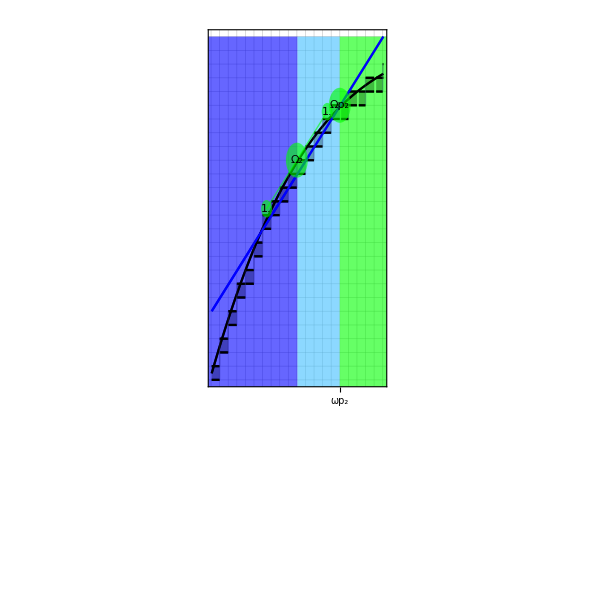

```mathematica
dist=setUpErf[ 20,128,{{0,255},{0,255}},Unit->False,G->False];
rangesTest={ dist["ranges"][[1,1]],Sequence@@Delete[ dist["ticks"][[2,All,1]],3], dist["ranges"][[1,2]]};
testBg=CheckerBoardFromList[rangesTest, dist["ranges"][[2]],
Map[{( dist["color"]@@#1)}&,Map[{#,1}&,(Rest[rangesTest]+Most[rangesTest])/2]],
{{"Disgard"},{"Redistribute"},{"Keep"},{"Redistribute"},{"Disgard"}}
,{0,-1},{0,1},0.8];
circSize={0.005,0.005}( dist["ranges"][[1,2]]- dist["ranges"][[1,1]]);
 Omega={dist["param"] [[4,2,2]],dist["func"][dist["param"] [[4,2,2]]]};
OmegaP={dist["param"] [[5,2,2]],dist["func"][dist["param"] [[5,2,2]]]};
plt=Plot[{ dist["func"][x],Ceiling[dist["func"][Floor[x]]],Floor[dist["func"][Floor[x]]],dist["linearExtensionFunc"][x]},{x,dist["param"] [[4,2,2]]-10,dist["param"] [[4,2,2]]+10},Frame->True,PlotStyle->{Black,Black,Black,Blue},Filling->{2->{3}},FrameTicks->{ {BinaryTicks[dist["ranges"][[2,1]],dist["ranges"][[2,2]],3],None},{MixTicks[Map[{#[[1]],#[[2]]/256}&,BinaryTicks[dist["ranges"][[1,1]],dist["ranges"][[1,2]],5]], dist["ticks"][[1]],10],
MixTicks[BinaryTicks[dist["ranges"][[1,1]],dist["ranges"][[1,2]],5], dist["ticks"][[2]],10] }},
Epilog->{
LabelPointGrad[ Omega[[1]], dist["func"][#1] &,"Ω_2",Green,{0,0},5,circSize ],
LabelPoint[ OmegaP[[1]], dist["func"][#1] &,"Ωp_2",Green,{0,0},circSize ]},AspectRatio->1,GridLines->{Table[i,{i,Floor[dist["param"] [[4,2,2]]]-10,Ceiling[dist["param"] [[4,2,2]]]+10,1}],Table[i,{i,Floor[Omega[[2]]]-15,Ceiling[Omega[[2]]]+10,1}]}];
Show[plt,Graphics[{Opacity[0.15],testBg}],plt]
```

we wish to find the intersection in the green zone of the cord with the distribution function as this is where the non unit gradient affects the discrete values allowing us to extend the value of ω. This is however not anylitically soluable so a numerical solution is found by solveing

(x-Ω_2)+Floor[dis[Ω_2]] == dis[x]

```mathematica
TraditionalForm[(x-Subscript[Ω, 2])+Floor[dis[Subscript[Ω, 2]]] == dis[x]]
```

Floor[dis(Ω_2)]+x-Ω_2==dis(x)

```mathematica
Simplify[x +dis["func"][Ω[[2]]]- Ω[[2]]-1]
```

```mathematica
N[dist["param"] [[4,2,1]]]
```

86.1155

```mathematica
Ωp={0,0};
Ωp[[2]]=Round[x/.NSolve[analytic["linearExtensionFunc"][x]==analytic["func"][x]&&x≥ analytic["param"] [[4,2,2]],x,Reals]][[1]]
Ωp[[1]]=Round[analytic["param"] [[4,2,1]]]-(Ωp[[2]]-Round[analytic["param"] [[4,2,2]]])
```

x/.NSolve[-1+dMin-tMin+x+((dMax-dMin) (Erf[μ/(√2 σ)]+Erf[√Log[((dMax-dMin) √(2/π))/((tMax-tMin) σ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]))]]))/(-Erf[(-1+μ)/(√2 σ)]+Erf[μ/(√2 σ)])-(tMax-tMin) (μ+σ √(Log[2/π]+2 Log[(-dMax+dMin)/((tMax-tMin) σ (Erf[(-1+μ)/(√2 σ)]-Erf[μ/(√2 σ)]))]))==dMin-((dMax-dMin) (Erf[μ/(√2 σ)]+Erf[(-tMin+x-(tMax-tMin) μ)/(√2 (tMax-tMin) σ)]))/(-Erf[μ/(√2 σ)]+Erf[(-tMax+tMin+(tMax-tMin) μ)/(√2 (tMax-tMin) σ)])&&x≥tMin+(tMax-tMin) (μ+√2 σ √Log[((dMax-dMin) √(2/π))/((tMax-tMin) σ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]))]),x,Reals]

-(x/.NSolve[-1+dMin-tMin+x+((dMax-dMin) (Erf[μ/(√2 σ)]+Erf[√Log[((dMax-dMin) √(2/π))/((tMax-tMin) σ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]))]]))/(-Erf[(-1+μ)/(√2 σ)]+Erf[μ/(√2 σ)])-(tMax-tMin) (μ+σ √(Log[2/π]+2 Log[(-dMax+dMin)/((tMax-tMin) σ (Erf[(-1+μ)/(√2 σ)]-Erf[μ/(√2 σ)]))]))==dMin-((dMax-dMin) (Erf[μ/(√2 σ)]+Erf[(-tMin+x-(tMax-tMin) μ)/(√2 (tMax-tMin) σ)]))/(-Erf[μ/(√2 σ)]+Erf[(-tMax+tMin+(tMax-tMin) μ)/(√2 (tMax-tMin) σ)])&&x≥tMin+(tMax-tMin) (μ+√2 σ √Log[((dMax-dMin) √(2/π))/((tMax-tMin) σ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]))]),x,Reals])+Round[tMin+(tMax-tMin) (μ-√2 σ √Log[((dMax-dMin) √(2/π))/((tMax-tMin) σ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]))])]+Round[tMin+(tMax-tMin) (μ+√2 σ √Log[((dMax-dMin) √(2/π))/((tMax-tMin) σ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]))])]

```mathematica
uUnitGrad[ σ,μ,{{sMin,sMax},{dMin,dMax}}][[2]]
```

μ+σ √(Log[2/π]+2 Log[(dMax-dMin)/(sMax-sMin)]-2 Log[σ (-Erf[(-1+μ)/(√2 σ)]+Erf[μ/(√2 σ)])])

### The Effectivly constant range

We are interested in where the function equals dMin + 1 and dMax - 1 because here the function can be replaced with a simple range test.

For efficiency it is useful to have the values at which upon rounding the function is constant. This is where the function equals dL = {1/dRange, 1 - 1/dRange}.

```mathematica
Clear[uErfLowHigh,μ,σ,sMin,sMax,dMin,dMax]
```

```mathematica
Clear[uErfLowHigh,μ,σ,sMin,sMax,dMin,dMax]
FullSimplify[eErf[ x,γ,μ,0,1,0,1]]==dL
uErfLowHighf=Function[{dL,γ,μ},Evaluate[FullSimplify[(x/.(Solve[%,x,InverseFunctions->True]/. C[1]->0))[[1]]] ]];
uErfLowHighf[ dL,γ,μ]
```

```mathematica
μ+InverseErf[(dL-1) Erf[γ μ]+dL Erf[γ(1-μ)]]/γ
```

dL = {1/dRange, 1 - 1/dRange}. Let  dΔ = 1/dRange then dL = {dΔ, 1 - dΔ}

```mathematica
{μ+InverseErf[(dΔ-1) Erf[γ μ]+dΔ Erf[γ(1-μ)]]/γ,μ+InverseErf[(1-dΔ-1) Erf[γ μ]+(1-dΔ) Erf[γ(1-μ)]]/γ}
```

```mathematica
tableGammaFuncs=Function[{vars,ranges},
{{μ,c},{σ,s},{γ,g}}=vars;
{{sMin,sMax},{dMin,dMax}}=ranges;Grid[{{
Plot[peakNormedNormalDistribution[pointToUnit[c,{sMin,sMax}],scaleToUnit[s,{sMin,sMax}],t],{t,0,1},PlotRange->{{0,1},Automatic},ImageSize->{200,200}],
Plot[peakNormedNormalDistribution[c,s,t],{t,sMin,sMax},PlotRange->{{sMin,sMax},All},ImageSize->{200,200}]},{Plot[PDF[NormalDistribution[pointToUnit[c,{sMin,sMax}],scaleToUnit[s,{sMin,sMax}]],t],{t,0,1},PlotRange->{{0,1},Automatic},ImageSize->{200,200}],
Plot[PDF[NormalDistribution[c,s],t],{t,sMin,sMax},PlotRange->{{sMin,sMax},All},ImageSize->{200,200}]}}]
]
```

```mathematica
FullSimplify[{uErfLowHighf[ 1/(dMax-dMin),γ,μ],
uErfLowHighf[((dMax-dMin)- 1)/(dMax-dMin),γ,μ]}]
```

```mathematica
uErfLowHigh[ γ_,μ_,{{sMin_,sMax_},{dMin_,dMax_}}]:={μ+InverseErf[((1-dMax+dMin) Erf[γ μ]+Erf[γ-γ μ])/(dMax-dMin)]/γ,μ+InverseErf[(-Erf[γ μ]+(-1+dMax-dMin) Erf[γ-γ μ])/(dMax-dMin)]/γ}
```

```mathematica
Row[{"Λ = ",TraditionalForm[uErfLowHigh[ γ,μ,{{sMin,sMax},{dMin,dMax}}]]}]
```

Λ = {(erf^-1(((-dMax+dMin+1) erf(γ μ)+erf(γ-γ μ))/(dMax-dMin)))/γ+μ,(erf^-1(((dMax-dMin-1) erf(γ-γ μ)-erf(γ μ))/(dMax-dMin)))/γ+μ}

```mathematica
DynamicDistroPanel[{
({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;{{sRange,dRange,κ},{δ,m},{λ,L},{ω,Ω}}=#3; 
         fun[x_]:=eErf[ x,g,c,sMin,sMax,dMin,dMax];
center={c,fun[c]};
Column[{Panel[Dynamic[Style[StringJoin["The gradient at the mean is ",ToString[m]],Bold]], ImageSize -> Scaled[1], Alignment -> Center,Background->LightBlue],Panel[Dynamic[Style[If[Length[Ω]>1,StringJoin["The gradient is one at ",ToString[Ω[[1]]]," and ",ToString[Ω[[2]]]],"The gradient is never one"],Bold]], ImageSize -> Scaled[1], Alignment -> Center,Background->LightGreen],
Panel[Dynamic[Style[StringJoin["The distribution is effectivly flat between : 0 - ",ToString[L[[1]]]," and ",ToString[L[[2]]], " - ",ToString[sMax]],Bold]], ImageSize -> Scaled[1], Alignment -> Center,Background->LightRed]}]
)&,(Plot[{
fun[x], 
m*(x-c) + center[[2]]
}, {x, 0, 255}, Frame -> True, PlotRange -> {{sMin, sMax},{dMin, dMax}}, AspectRatio->(dMax-dMin)/(sMax-sMin),Background->White,
Epilog->{
 LabelPointGrad[c, fun[#1] & , NumberForm[m,3],Blue,{0,-1},20],
If[Length[Ω]>1, LabelPointGrad[Ω[[1]],fun[#1] &,Round[Ω[[1]]],Green,{0,0},20]],
If[Length[Ω]>1, LabelPointGrad[Ω[[2]],fun[#1] &,Round[Ω[[2]]],Green,{0,0},20]],
 LabelPoint[L[[1]],fun[#1] &,L[[1]],Red,{0,-1}],
 LabelPoint[L[[2]],fun[#1] &,L[[2]],Red,{0,1}]
}])&},Panel[Column[{#1,
Row[{Panel[#2,ImageSize->Scaled[.23],Alignment->Center],"  ",Panel[#3[[1]],ImageSize->Scaled[.74],Alignment->Center]}],Panel[#3[[2]],ImageSize->{Scaled[1],Scaled[1]},Alignment->Center]
},Center],ImageSize->Scaled[0.6]]&]
```

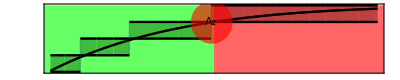

```mathematica
dist=setUpErf[ 20,128,{{0,255},{0,255}},Unit->False,G->False];
rangesTest={ dist["ranges"][[1,1]],Sequence@@Delete[ dist["ticks"][[2,All,1]],3], dist["ranges"][[1,2]]};
testBg=CheckerBoardFromList[rangesTest, dist["ranges"][[2]],
Map[{( dist["color"]@@#1)}&,Map[{#,1}&,(Rest[rangesTest]+Most[rangesTest])/2]],
{{"Disgard"},{"Redistribute"},{"Keep"},{"Redistribute"},{"Disgard"}}
,{0,-1},{0,1},0.8];
circSize={0.005,0.005}( dist["ranges"][[1,2]]- dist["ranges"][[1,1]]);
 Lambda={dist["param"] [[3,2,2]],dist["func"][dist["param"] [[3,2,2]]]};
plt=Plot[{ dist["func"][x],Ceiling[dist["func"][Ceiling[x]]],Floor[dist["func"][Ceiling[x]]]},{x,dist["param"] [[3,2,2]]-10,dist["param"] [[3,2,2]]+10},Frame->True,PlotStyle->{Black,Black,Black,Blue},Filling->{2->{3}},FrameTicks->{ {BinaryTicks[dist["ranges"][[2,1]],dist["ranges"][[2,2]],3],None},{MixTicks[Map[{#[[1]],#[[2]]/256}&,BinaryTicks[dist["ranges"][[1,1]],dist["ranges"][[1,2]],5]], dist["ticks"][[1]],10],
MixTicks[BinaryTicks[dist["ranges"][[1,1]],dist["ranges"][[1,2]],5], dist["ticks"][[2]],10] }},
PlotPoints->1000,
Epilog->{
LabelPoint[ Lambda[[1]], dist["func"][#1] &,"Λ_2",Red,{0,0},circSize ]},AspectRatio->1,GridLines->{Table[i,{i,Floor[Lambda[[1]]]-10,Ceiling[Lambda[[1]]]+10,1}],Table[i,{i,Floor[Lambda[[2]]]-15,Ceiling[Lambda[[2]]]+1,1}]}];
Show[plt,Graphics[{Opacity[0.15],testBg}],plt,AspectRatio->1/5]
```

#### The compact distribution.

| 0-1 | sMin - sMax
Mean | (c-sMin)/(sMax-sMin) | c
Std | s/(sMax-sMin) | s
G | (sMax-sMin)/(√2 s) | 1/(√2 s)

| 0-1 | sMin - sMax
Mean | (c-sMin)/(sMax-sMin) | c
Std | 1/(√2 g (sMax-sMin)) | 1/(√2 g)
G | g (sMax-sMin) | g

| 0-1 | sMin - sMax
Mean | μ | sMin+(sMax-sMin) μ
Std | σ | (sMax-sMin) σ
G | 1/(√2 σ) | 1/(√2 (sMax-sMin) σ)

| 0-1 | sMin - sMax
Mean | μ | sMin+(sMax-sMin) μ
Std | 1/(√2 γ) | (sMax-sMin)/(√2 γ)
G | γ | γ/(sMax-sMin)

```mathematica
Clear[setUpErf,unitGrad]
setUpErf[ σsγg_,μc_,{{sMin_,sMax_},{dMin_,dMax_}},opts:OptionsPattern[]]:= Module[{x,μ,c,σ,s,γ,g,sRange,dRange,κ,δ,m,λ,Λ,ω,Ω,ωp,Ωp,linear,shift,dis,sPts,pts,tickstyle},
{{μ,c},{σ,s},{γ,g}}= setDistroValues[ σsγg,μc,{{sMin,sMax},{dMin,dMax}},opts];
{{sRange,dRange,κ},{δ,m},{λ,Λ},{ω,Ω}}=setDistroParams[ {{μ,c},{σ,s},{γ,g}},{{sMin,sMax},{dMin,dMax}}];
dis["vars"]={{μ,c},{σ,s},{γ,g}};
dis["ranges"]={{sMin,sMax},{dMin,dMax}};
dis["param"]={{sRange,dRange,κ},{δ,m},{λ,Λ},{ω,Ω}};
dis["func"]=Function[{x},Evaluate[dMin-dRange(Erf[g (c-sMin)]+Erf[g (x-c)])/(Erf[g (c-sMax)]+Erf[g (sMin-c)])],Listable];
dis["keepQ"]=δ/κ > 1;

dis["linearExtensionFunc"]=Function[{x},Evaluate[Simplify[x +Floor[dis["func"][Ω[[2]]]]- Ω[[2]]-1]]];
If[dis["keepQ"],
Ωp={0,0};
Ωp[[2]]=Round[x/.NSolve[dis["linearExtensionFunc"][x]==dis["func"][x]&&x≥ Ω [[2]],x,Reals,WorkingPrecision->1]][[1]];
Ωp[[1]]=Round[Ω [[1]]]-(Ωp[[2]]-Round[Ω [[2]]]);
dis["redistributeQ"]={Ωp[[1]]> Λ[[1]]+1,Ωp[[2]]< Λ[[2]]-1};
If[Not[dis["redistributeQ"][[2]]], Ωp[[2]]= Λ[[2]]];
If[Not[dis["redistributeQ"][[1]]], Ωp[[1]]= Λ[[1]]];
ωp=pointToUnit[Ωp,{sMin,sMax}];
dis["param"]={{sRange,dRange,κ},{δ,m},{λ,Λ},{ω,Ω},{ωp,Ωp}};
dis["extendedKeepQ"]={Ωp[[1]]< Ω [[1]],Ωp[[2]]> Ω [[2]]};,
dis["redistributeQ"]={True,True};
dis["extendedKeepQ"]={False,False};
];
dis["disgardQ"]= {Round[Λ[[1]]]>sMin+1,Round[Λ[[2]]]<sMax-1};

dis["selectRegions"]=Function[{list},Evaluate[ReleaseHold@{
If[dis["disgardQ"][[1]],            list[[1]],Hold[Sequence[]]],
If[dis["redistributeQ"][[1]],list[[2]], Hold[Sequence[]]],
If[dis["extendedKeepQ"][[1]],list[[3]],Hold[Sequence[]]],
If[dis["keepQ"],                              list[[4]],Hold[Sequence[]]],
If[dis["extendedKeepQ"][[2]],list[[5]],Hold[Sequence[]]],
If[dis["redistributeQ"][[2]],list[[6]], Hold[Sequence[]]],
If[dis["disgardQ"][[2]],           list[[7]], Hold[Sequence[]]]}
]];

dis["regionNames"]= dis["selectRegions"][
{"Disgard","Redistribute","Extended Keep","Keep","Extended Keep","Redistribute","Disgard"}];
dis["numRegions"]=Length[dis["regionNames"]];

bounds=Table[0,{i,1,dis["numRegions"]+1}];
syms=Table[column[""],{i,1,dis["numRegions"]+1}];
i=1;
syms[[i]]=column["tMin"]; bounds[[i]]=sMin;
If[dis["disgardQ"][[1]],            i++;syms[[i]]=column["Λ_1"];   bounds[[i]]=N[Λ[[1]]],   AppendTo[syms[[i]],"Λ_1"] ];
If[dis["redistributeQ"][[1]] ,i++;syms[[i]]=column["Ωp_1"]; bounds[[i]]=N[Ωp[[1]]],AppendTo[syms[[i]],"Ωp_1"]];
If[dis["extendedKeepQ"][[1]],i++;syms[[i]]=column["Ω_1"];    bounds[[i]]=N[Ω[[1]]],  AppendTo[syms[[i]],"Ω_1"]];
If[dis["keepQ"],                              i++;syms[[i]]=column["Ω_2"];    bounds[[i]]=N[Ω[[2]]],  AppendTo[syms[[i]],"Ω_2"]];
If[dis["extendedKeepQ"][[2]],i++;syms[[i]]=column["Ωp_2"];  bounds[[i]]=N[Ωp[[2]]],AppendTo[syms[[i]],"Ωp_2"]];
If[dis["redistributeQ"][[2]],i++;syms[[i]]=column["Λ_2"];     bounds[[i]]=N[Λ[[2]]],  AppendTo[syms[[i]],"Λ_2"]];
If[dis["disgardQ"][[2]],            i++;syms[[i]]=column["tMax"];bounds[[i]]=sMax,             AppendTo[syms[[i]],"tMax"]];
dis["regionSymbols"]={syms//.{column[list__]:> Column[{list}],
"Λ_1"-> "λ_1","Λ_2"-> "λ_2","Ωp_1"->"ωp_1","Ωp_2"->"ωp_2" ,"Ω_1"->"ω_1" ,"Ω_2"->"ω_2" ,"tMin"->0,"tMax"-> 1 },syms/.column[list__]:> Column[{list}]};
dis["regionBounds"]=bounds;
tickstyle[pos_,txt_]:={pos,  Style[txt,   Bold,Background->None],{0.03,0.01}} ;
dis["ticks"]={Insert[MapThread[tickstyle,{dis["regionBounds"],dis["regionSymbols"][[1]]}],tickstyle[N[c],"μ"],Round[dis["numRegions"]/2]+1],
Insert[MapThread[tickstyle ,{dis["regionBounds"],dis["regionSymbols"][[2]]}],tickstyle[N[c],"C"],Round[dis["numRegions"]/2]+1]};

dis["opacity"]=0.6;
If[TrueQ[δ/κ < 1],
dis["piecewise"]=Function[{x},Evaluate[Piecewise[{
    {dMin,                                            x<Λ[[1]]}
,{dis["func"][x],Λ[[1]]<=x<Λ[[2]]}
,{dMax,                       Λ[[2]]≤x }}]],Listable];;
dis["color"]=Function[{x,y},Piecewise[{
    {Opacity[dis["opacity"],Red],                                       x<Λ[[1]]}
,{Opacity[dis["opacity"],Green],  Λ[[1]]≤x<Λ[[2]]}
,{Opacity[dis["opacity"],Red],       Λ[[2]]≤x}}]],
linear= Function[{x},Evaluate[x + dis["func"][ Ωp[[1]] ] - Ωp[[1]] ]];
shift=dis["func"][ Ωp[[2]] ]-linear[Ωp[[2]]];
dis["piecewise"]=Function[{x},Evaluate[Piecewise[dis["selectRegions"][{
    {dMin,                                                           x<Λ[[1]]}
,{dis["func"][x],               Λ[[1]]<=x<Ωp[[1]]}
,{linear[x],                         Ωp[[1]]<=x<Ω[[1]]}
,{linear[x],                           Ω[[1]]<=x<Ω[[2]]}
,{linear[x],                           Ω[[2]]<=x<Ωp[[2]]}
,{dis["func"][x]-shift,Ωp[[2]]<=x<Λ[[2]]}
,{dMax -shift,                      Λ[[2]]≤x}}]]],Listable];
dis["color"]=Function[{x,y},Evaluate[Piecewise[dis["selectRegions"][{
    {Opacity[dis["opacity"],Red],                       x<Λ[[1]]}
,{Opacity[dis["opacity"],Green],Λ[[1]]≤x<Ωp[[1]]}
,{Opacity[dis["opacity"],RGBColor[0.25,0.75,1]],Ωp[[1]]≤x<Ω[[1]]}
,{Opacity[dis["opacity"],Blue],  Ω[[1]]≤x<Ω[[2]]}
,{Opacity[dis["opacity"],RGBColor[0.25,0.75,1]],Ω[[2]]≤x<Ωp[[2]]}
,{Opacity[dis["opacity"],Green],Ωp[[2]]≤x<Λ[[2]]}
,{Opacity[dis["opacity"],Red],     Λ[[2]]≤x}}]]
]]
];
sPts=Sort[Flatten[{Ω,Λ}]];
dis["pts"]=Transpose[{sPts,dis["func"][sPts]}];
dis
]
```

```mathematica
Clear[AlternateTicks];
AlternateTicks[ticks_,topQ_:False]:=Module[{out,top,bottom},out=ticks;
If[topQ,  
top="";bottom=Graphics[{Line[{{0,0},{0,0.1}}]}];,
top=Graphics[{Line[{{0,0},{0,0.1}}]}]; bottom="";
];Do[If[OddQ[i],out[[i,2]]=Column[{top,ticks[[i,2]]},Center,0],out[[i,2]]=Column[{ticks[[i,2]],bottom },Center,0]],{i,1,Length[ticks]}];out]
```

```mathematica
DistroPlot[dist_]:=Module[{testBg,circSize,plt,usePiecewise},
usePiecewise=dist["piecewise"][dist["ranges"][[1,2]]]<.98dist["ranges"][[2,2]];
testBg=CheckerBoardFromList[dist["regionBounds"], dist["ranges"][[2]],
dist["selectRegions"][{
{Opacity[dist["opacity"],Red]},{Opacity[dist["opacity"],Green]},
{Opacity[dist["opacity"],RGBColor[0.25,0.75,1]]},{Opacity[dist["opacity"],Blue]},{Opacity[dist["opacity"],RGBColor[0.25,0.75,1]]},{Opacity[dist["opacity"],Green]},
{Opacity[dist["opacity"],Red]}}],
Map[List,dist["regionNames"]]
,{0,-0.6},{0,1},0.8];
circSize={0.02,0.02}( dist["ranges"][[1,2]]- dist["ranges"][[1,1]]);
plt=Plot[Evaluate[If[usePiecewise,{ dist["func"][x], dist["piecewise"][x]},dist["func"][x]]],{x,dist["ranges"][[1,1]],dist["ranges"][[1,2]]},Frame->True,PlotStyle->{Black,Black},FrameTicks->{ {BinaryTicks[dist["ranges"][[2,1]],dist["ranges"][[2,2]],3],None},{MixTicks[Map[{#[[1]],#[[2]]/256}&,BinaryTicks[dist["ranges"][[1,1]],dist["ranges"][[1,2]],5]], AlternateTicks[dist["ticks"][[1]],False ],10],
MixTicks[BinaryTicks[dist["ranges"][[1,1]],dist["ranges"][[1,2]],5], AlternateTicks[dist["ticks"][[2]],True ],10] }},
Epilog->{
LabelPointGrad[ dist["vars"] [[1,2]], dist["func"][#1] &,Round[ dist["vars"] [[1,2]]],Blue,{0,0},11,circSize ],
LabelPointGrad[ dist["param"] [[4,2,1]], dist["func"][#1] &,Round[ dist["param"] [[4,2,1]]],Green,{0,0},11,circSize ],
LabelPointGrad[ dist["param"] [[4,2,2]], dist["func"][#1] &,Round[ dist["param"] [[4,2,2]]],Green,{0,0},11,circSize ],
LabelPoint[ dist["param"] [[3,2,1]], dist["func"][#1] &,Round[ dist["param"] [[3,2,1]]],Red,{0,0},circSize ],
LabelPoint[ dist["param"] [[3,2,2]], dist["func"][#1] &,Round[ dist["param"] [[3,2,2]]],Red,{0,0},circSize ],
Inset[Panel[valTable[ dist["vars"], dist["ranges"]],Background->Opacity[0.5,White]],Scaled[{.05,.9}],Scaled[{0,1}]],
Text[If[usePiecewise,"Compact Distribution",""],{ dist["ranges"][[1,2]], dist["piecewise"][ dist["ranges"][[1,2]]]},{1,1}],
Text["Full Range Distribution",{ dist["ranges"][[1,2]], dist["func"][ dist["ranges"][[1,2]]]},{1,1}]},AspectRatio->1];
Show[plt,Graphics[{Opacity[0.15],testBg}],plt]
]
```

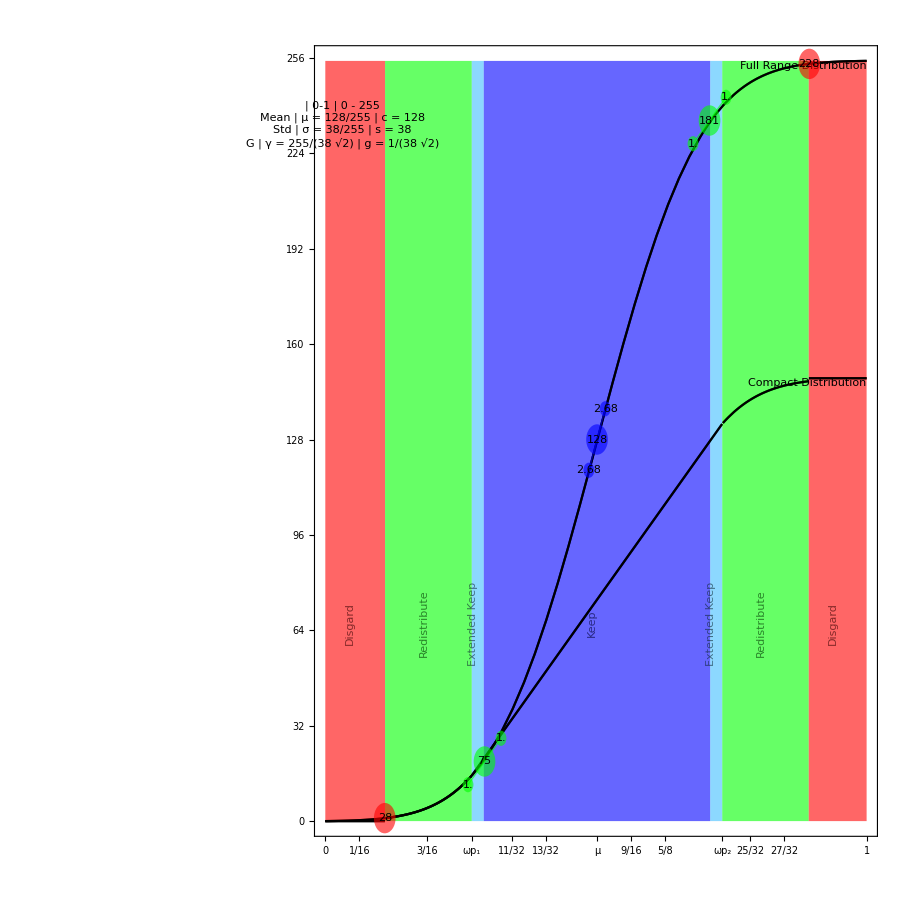

```mathematica
test=setUpErf[ 38,128,{{0,255},{0,255}},Unit->False,G->False];
DistroPlot[test]
```

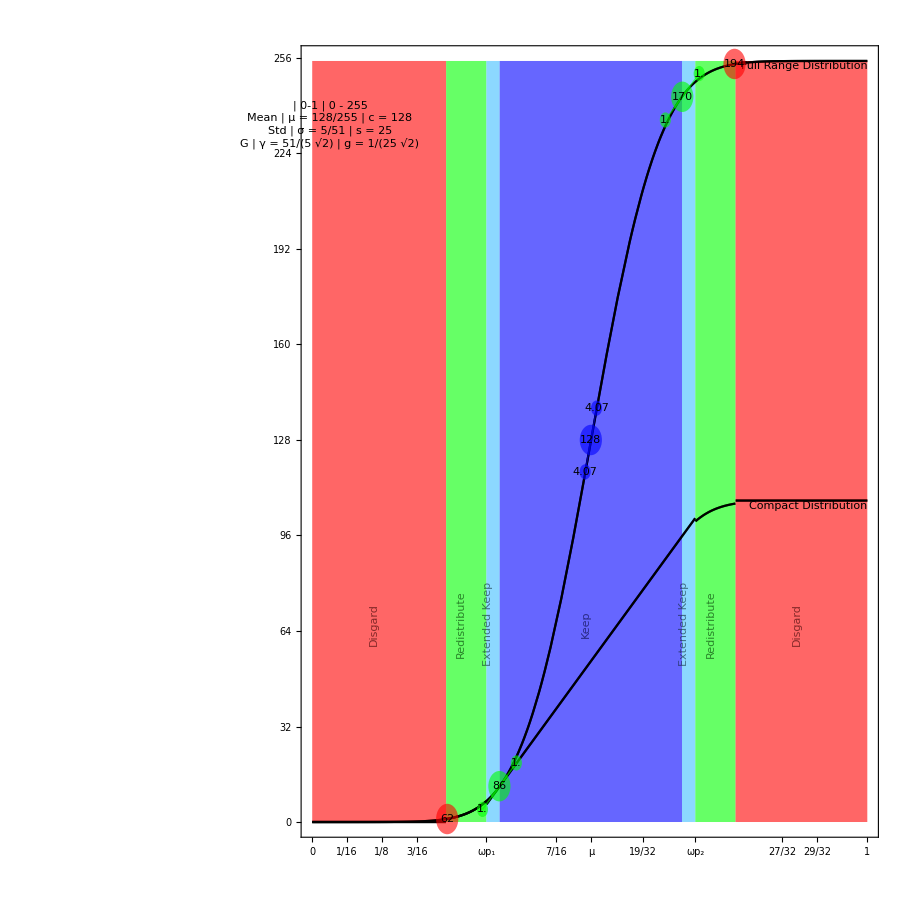

```mathematica
DistroPlot[test]
```

```mathematica
RGBColor[0.25,0.75,1]
```

-Graphics-

```mathematica
Plot[{test["func"][x],test["piecewise"][x]},{x,0,255},ColorFunction->test["color"],ColorFunctionScaling->False,Frame->True,FrameTicks->{ {BinaryTicks[0,255,3],None},{MixTicks[Map[{#[[1]],#[[2]]/256}&,BinaryTicks[0,255,5]],test["ticks"][[1]],10],
MixTicks[BinaryTicks[0,255,5],test["ticks"][[2]],10] }},AspectRatio->1]
```

-Graphics-

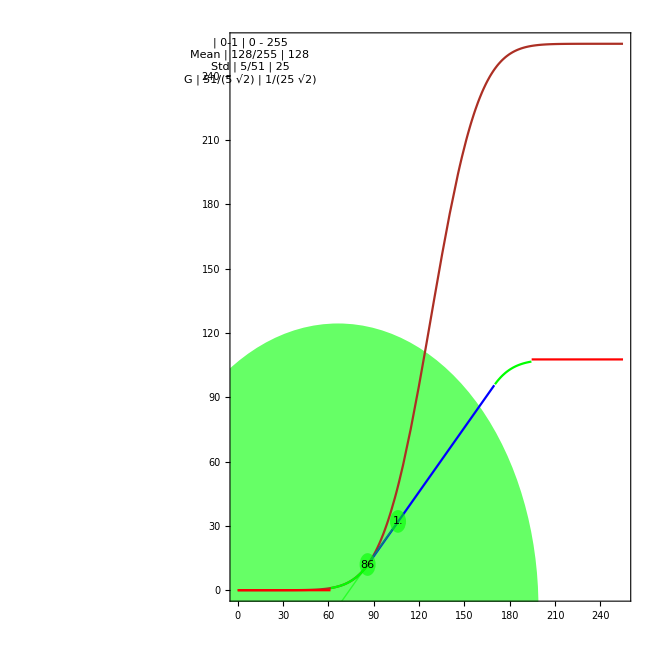

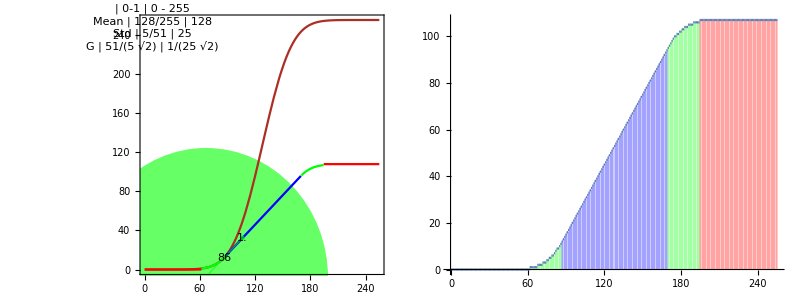

```mathematica
test=setUpErf[ 25,128,{{0,255},{0,255}},Unit->False,G->False];
Plot[{test["func"][x],test["piecewise"][x]},{x,0,255},ColorFunction->test["color"],ColorFunctionScaling->False,Frame->True,FrameTicks->{ {All,None},{All,{Sequence@@BinaryTicks[0,255,3],Sequence@@test["ticks"]}}},Epilog->{LabelPointGrad[test["param"] [[4,2,1]],test["func"][#1] &,Round[test["param"] [[4,2,1]]],Green,{0,0},20,Scaled[{0.02,0.02}]],Inset[Panel[valTable[test["vars"],test["ranges"]]],Scaled[{.05,.95}],Scaled[{0,1}]]},AspectRatio->1]
Grid[{{Plot[{test["func"][x],test["piecewise"][x]},{x,0,255},ColorFunction->test["color"],ColorFunctionScaling->False,Frame->True,FrameTicks->{ {All,None},{All,{Sequence@@BinaryTicks[0,255,3],Sequence@@test["ticks"]}}},Epilog->{LabelPointGrad[test["param"] [[4,2,1]],test["func"][#1] &,Round[test["param"] [[4,2,1]]],Green,{0,0},20,Scaled[{0.01,0.01}]],Inset[Panel[valTable[test["vars"],test["ranges"]]],Scaled[{.05,.95}],Scaled[{0,1}]]}],
DiscretePlot[Evaluate[Floor[test["piecewise"][x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->test["color"],ColorFunctionScaling->False,Joined->False]}}]
```

### Values from MatLAB

```mathematica
γMatLAB = {γMin/2,18.0312,2.8680};
μMatLAB = {128.0000,125.4850,107.3765}/255;
```

```mathematica
matLab=Table[setUpErf[ γMatLAB[[i]],μMatLAB[[i]],{{0,255},{0,255}},Unit->True,G->True],{i,1,3}];
```

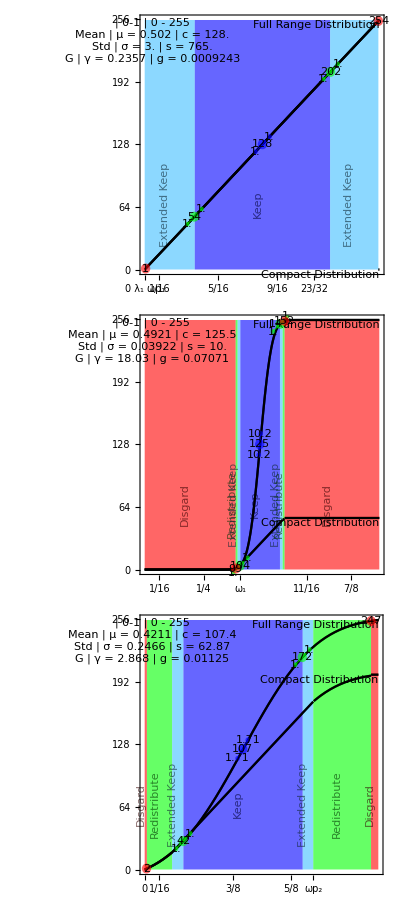

```mathematica
Grid[Table[{DistroPlot[matLab[[i]]]},{i,1,3}]]
```

```mathematica
pnt,text,m,line,theta
```

```mathematica
Clear[ LabelPointGrad];
 LabelPointGrad[x_,fun_,txt_:"",color_:Green,align_:{0,0},len_:40,size_:12]:=Block[{},
pnt=Round[N[{x,fun[x]}]];
m=Function[{xx},Evaluate[D[fun[xx],xx]]];
theta=ArcTan[m[x]];
line=Function[{xx},Evaluate[ {xx Cos[theta], xx Sin[theta]} + pnt ]];
If[TrueQ[txt==""],text=StringJoin[ToString[pnt[[1]]],"  ",ToString[pnt[[2]]]],text=txt];{color,Opacity[0.6],
Disk[pnt,size],Disk[line[x+len],size/2],Disk[line[x-len], size/2],
Thick,Line[{line[x-len],line[x+len]}],
Black,Opacity[1],
Text[text,pnt,align,line[x+len]-line[x-len]],Text[ToString[NumberForm[N[m[x]],3]],line[x+len],{0,0},line[x+len]-line[x-len]],
Text[ToString[NumberForm[N[m[x]],3]],line[x-len],{0,0},line[x+len]-line[x-len]]}];
```

```mathematica
line
```

Function[{xx},{xx,{172+0.707107 xx,217+0.707107 xx}}]

```mathematica
theta
```

0.785398

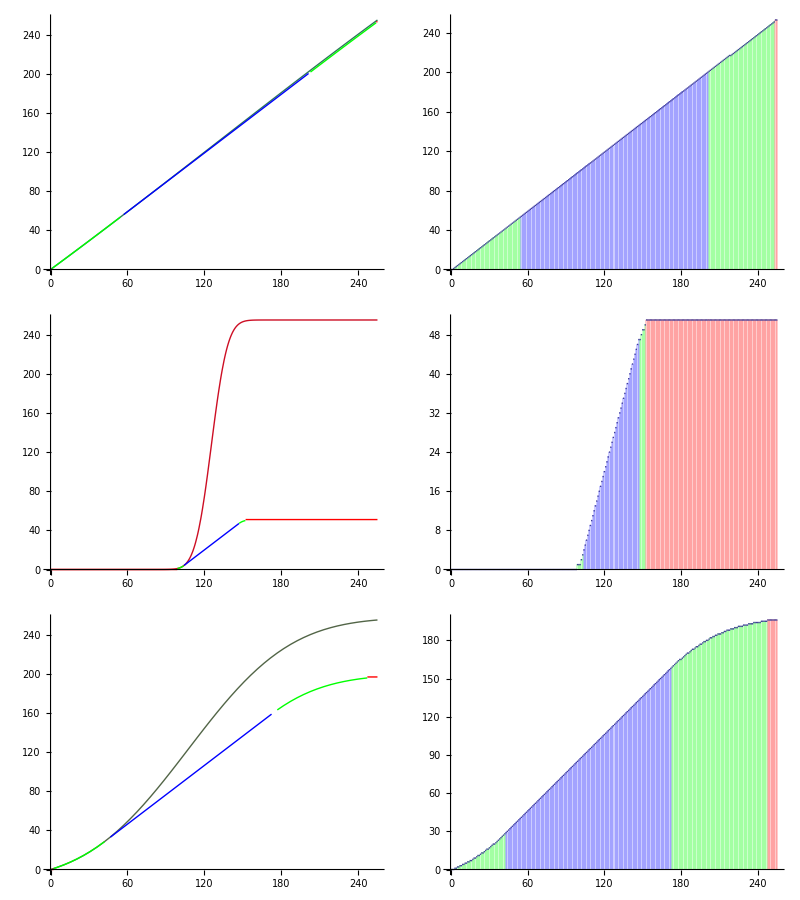

```mathematica
Grid[Table[{Plot[{matLab[[i]]["func"][x],matLab[[i]]["piecewise"][x]},{x,0,255},ColorFunction->matLab[[i]]["color"],ColorFunctionScaling->False,ImageSize->300],
DiscretePlot[Evaluate[Floor[matLab[[i]]["piecewise"][x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->matLab[[i]]["color"],ColorFunctionScaling->False,Joined->False,ImageSize->300]},{i,1,3}]]
```

```mathematica
setUprErf[ gMatLAB[[1]],cMatLAB[[1]],0,255,0,255]
Grid[{{Plot[{nErf[x],pErf[x]},{x,0,255},ColorFunction->Function[{x,y},pErfColor[x,y]],ColorFunctionScaling->False],
DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False]}}]
```

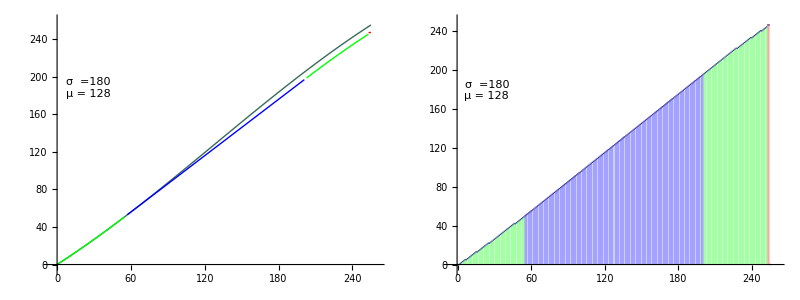

```mathematica
setUprErf[ gMatLAB[[2]],cMatLAB[[2]],0,255,0,255]
Grid[{{Plot[{nErf[x],pErf[x]},{x,0,255},ColorFunction->Function[{x,y},pErfColor[x,y]],ColorFunctionScaling->False],
DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False]}}]
```

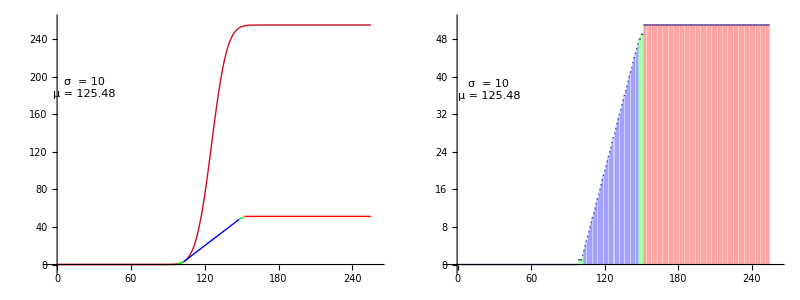

```mathematica
setUprErf[ gMatLAB[[3]],cMatLAB[[3]],0,255,0,255]
Grid[{{Plot[{nErf[x],pErf[x]},{x,0,255},ColorFunction->Function[{x,y},pErfColor[x,y]],ColorFunctionScaling->False],
DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False]}}]
```

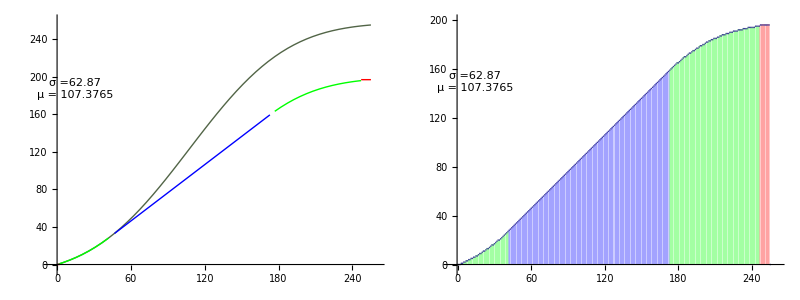

## Relationship to the Normal Distribution

We want to specify μ, σ, sMin, sMax, dMin, dMax for the space as these are the parameters which can be statistically found.
From these parameters we want to find g and c for the adjustable distribution above.
First we find a relationship to a gaussian on the axis.

```mathematica
Clear[μ,σ, g,c, sMin, sMax, dMin, dMax];
xScale =  1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[ (sMax - μ)/(√2 σ)]);
anyliticalErf[x_]:=Evaluate[FullSimplify[Integrate[ (dMax-dMin) PDF[NormalDistribution[μ,σ] ,xScale t],{t,sMin / xScale,x / xScale}]]+ dMin]
anyliticalErf[x]
```

Comparing to the adjustable distribution

```mathematica
Clear[μ,σ, g,c, sMin, sMax, dMin, dMax];
setUprErf[ g,c,sMin,sMax,dMin,dMax]
nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]};
%[[0]][%[[1]],Simplify[Together[%[[0]][%[[2]],%[[3]]]]]]
```

We can see the relationship of the average to c and the standard deviation to g.

```mathematica
μ =5;
σ =.2;
sMax = 8; sMin = 2;
dMin = 0; dMax= 2;

g =  (sMax-sMin)/(Sqrt[2] σ) ;
c = μ;

setUprErf[ g,c,sMin,sMax,dMin,dMax]
Plot[{anyliticalErf[x],PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,sMin, sMax},PlotRange->{{sMin, sMax},Automatic}]
```

```mathematica
g
```

```mathematica
Manipulate[
Plot[{Evaluate[g =  (sMax-sMin)/(Sqrt[2] σ) ;setUprErf[ g,μ,sMin,sMax,dMin,dMax]];nErf[x],anyliticalErf[x],(dMax-dMin) PDF[NormalDistribution[μ,σ],x]},{x,sMin,sMax},PlotStyle->{Blue,Green,Red},AxesLabel->TraditionalForm/@{a,iErf[a]},PlotRange->{{sMin,sMax},{dMin, dMax}},
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{{dMin,0},-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{μ,128},sMin,sMax,1,ValueThumbSlider[##]&},{{σ,0.5},0.0,10.0,ValueThumbSlider[##]&}
]
```

## Approximations to the Erf

A good approximation is found using continued fractions and the following numbers

```mathematica
Unprotect[Rationalize];
Options[Rationalize]={Precision->10^-12};
Protect[Rationalize];
```

```mathematica
Options[Rat]={Precision->10^-12};
a1=0.254829592;
A1[OptionsPattern[Rat]]:=Rationalize[a1,OptionValue[Precision]];
a2=0.284496736;
A2[OptionsPattern[Rat]]:=Rationalize[a2,OptionValue[Precision]];
a3=1.421413741;
A3[OptionsPattern[Rat]]:=Rationalize[a3,OptionValue[Precision]];
a4=1.453152027;
A4[OptionsPattern[Rat]]:=Rationalize[a4,OptionValue[Precision]];
a5=1.061405429;
A5[OptionsPattern[Rat]]:=Rationalize[a5,OptionValue[Precision]];
p=0.3275911;
P[OptionsPattern[Rat]]:=Rationalize[p,OptionValue[Precision]];
```

```mathematica
TableForm[{{"Precision","A1","A2","A3","A4","A5","P"},Sequence@@Table[pre=10^(-prec);{pre,A1[Precision->pre],A2[Precision->pre],A3[Precision->pre],A4[Precision->pre],A5[Precision->pre],P[Precision->pre]},{prec,1,12}]}]
```

The functional Approximation is formed thus

```mathematica
Clear[t,tt,erfP, erfH,erfA,error];
t[x_,opt___Rule]:=1/(1+P[opt] x)
t[a_,b_/;Not[TrueQ[Head[b]==Rule]],opt___Rule]:=b/(b+a*P[opt])
erfP[a_,b_,opt___Rule]:=(((((A5[opt]*t[a,b,opt]-A4[opt])*t[a,b,opt])+A3[opt])*t[a,b,opt]-A2[opt])*t[a,b,opt]+A1[opt])
erfH[a_,b_,opt___Rule]:=1-erfP[a,b,opt]*t[a,b,opt]*Exp[-1*a^2/b^2]
erfA[Times[a_,Power[b_,-1]],opt___Rule]:=Piecewise[{{erfH[a,b,opt],a/b≥0},{-erfH[-a,b],a/b<0}}]
erfA[a_,opt___Rule]:=Piecewise[{{erfH[a,1,opt],a≥0},{-erfH[-a,1],a<0}}]
erfA[a_,b_,opt___Rule]:=Piecewise[{{erfH[a,b,opt],a≥0},{-erfH[-a,b],a<0}}]
error[a_,opt___Rule]:=erfA[a,opt]-Erf[a];
```

```mathematica
Manipulate[
GraphicsRow[{Plot[erfA[x,Precision -> 10^(-prec) ],{x,-2,2},PlotStyle->{Blue},PlotRange->Automatic],
Plot[{error[x/1,Precision -> 10^(-prec)]},{x,-2,2},PlotRange->All]}],
{prec,0,12,1,ValueThumbSlider[##]&}]
```

## Distribution Function

```mathematica
rErf[x, g,c,0,255,0,2^16,Function[{a,b},erfA[a,b,Precision->10^-2]]]
```

```mathematica
Manipulate[
GraphicsRow[{Plot[{Floor[irErf[x, g,c,sMin,sMax,0,2^dMaxBits,Function[{a,b},erfA[a,b,Precision->10^(-precision)]]]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{0, 2^dMaxBits}},Filling->Bottom,PlotPoints->sMax-sMin+1,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,2^dMaxBits},{sMax,2^dMaxBits}}], Line[{{sMin,0},{sMax,0}}]}],
Plot[{rErf[x, g,c,sMin,sMax,0,2^dMaxBits,Function[{a,b},erfA[a,b,Precision->10^(-precision)]]] - rErf[x, g,c,sMin,sMax,0,2^dMaxBits]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->"Error",PlotRange->All,Filling->Axis,PlotPoints->sMax-sMin+1]}],{{precision,12},1,12,1,ValueThumbSlider[##]&},{{dMaxBits,16},1,64,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},1,10,ValueThumbSlider[##]&}
]
```

```mathematica
Clear[t,tt,erfP, erfH,erfA,error];
it[a_,b_,opt___Rule]:=b/(b+a*P[opt])
erfP[a_,b_,opt___Rule]:=(((((A5[opt]*t[a,b,opt]-A4[opt])*t[a,b,opt])+A3[opt])*t[a,b,opt]-A2[opt])*t[a,b,opt]+A1[opt])
erfH[a_,b_,opt___Rule]:=1-erfP[a,b,opt]*t[a,b,opt]*Exp[-1*a^2/b^2]
erfA[Times[a_,Power[b_,-1]],opt___Rule]:=Piecewise[{{erfH[a,b,opt],a/b≥0},{-erfH[-a,b],a/b<0}}]
erfA[a_,opt___Rule]:=Piecewise[{{erfH[a,1,opt],a≥0},{-erfH[-a,1],a<0}}]
erfA[a_,b_/;b≥0,opt___Rule]:=Piecewise[{{erfH[a,b,opt],a≥0},{-erfH[-a,b],a<0}}]
error[a_,opt___Rule]:=erfA[a,opt]-Erf[a];
```

```mathematica
Clear[erfH,erfHs,yRange]
erfH[a_]:=yRange-yRange(((((aa5 tt[a]-aa4) tt[a])+aa3) tt[a]-aa2) tt[a]+aa1) tt[a]
erfHs[a_]:=yRange-(((((aa5 yRange^(1/16) tt[a]-aa4 yRange^(1/16)) yRange^(1/16) tt[a])+aa3 yRange^(1/8) ) yRange^(1/8) tt[a]-aa2 yRange^(1/4)) yRange^(1/4) tt[a]+aa1 yRange^(1/2)) yRange^(1/2)tt[a]
```

```mathematica
Simplify[erfHs[x]]
Simplify[erfH[x]]
```

```mathematica
erfH[a_]:=yRange-yRange(((((aa5 it[a]-aa4) it[a])+aa3) it[a]-aa2) it[a]+aa1) it[a]*Exp[-1 a^2/xRange^2];
```

```mathematica
erfH[a_]:=yRange-((((( it[a,aa5N  yRange^(1/16),aa5D]-aa4 yRange^(1/16)) yRange^(1/16) it[a])+aa3 yRange^(1/8) ) yRange^(1/8) it[a]-aa2 yRange^(1/4)) yRange^(1/4) it[a]+aa1 yRange^(1/2)) yRange^(1/2)it[a];
```

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,xMin_,xMax_,yMin_,yMax_,prec_]:=Module[{aa5,aa4,aa3,aa2,aa1,ppD,ppN},
Clear[yRange,xRange, erfN,erfD, it,erfH,rErf];
yRange = yMax-yMin;
xRange = xMax-xMin;
erfN = Erf[g (c-xMin)/xRange];
erfD = Erf[g (-c+xMax)/xRange]+Erf[g (c-xMin)/xRange];
ReplaceAll[
Unevaluated[
it[a_,n_,d_]:= n ppD xRange/(d(ppD xRange+a ppN));
erfH[a_]:=yRange-((((( it[a,aa4D aa5N  yRange^(1/16),aa5D]-aa4N yRange^(1/16))  it[a,aa3D yRange^(1/16),aa4D])+aa3N yRange^(1/8) )  it[a, aa2D yRange^(1/8), aa3D]-aa2N yRange^(1/4))  it[a,aa1D yRange^(1/4),aa2D]+aa1N yRange^(1/2))it[a, yRange^(1/2),aa1D];
rErf[x_]:=yMin+(   ( Sign[x-c]  erfH[grad Abs[x-const]] + yRange erfN))/ erfD;]
,{ppN->Numerator[P[Precision->prec]],ppD->Denominator[P[Precision->prec]],aa1->A1[Precision->prec],aa2->A2[Precision->prec],aa3->A3[Precision->prec],aa4->A4[Precision->prec],aa5->A5[Precision->prec],
aa1N->Numerator[A1[Precision->prec]],aa2N->Numerator[A2[Precision->prec]],aa3N->Numerator[A3[Precision->prec]],aa4N->Numerator[A4[Precision->prec]],aa5N->Numerator[A5[Precision->prec]], 
aa1D->Denominator[A1[Precision->prec]],aa2D->Denominator[A2[Precision->prec]],aa3D->Denominator[A3[Precision->prec]],aa4D->Denominator[A4[Precision->prec]],aa5D->Denominator[A5[Precision->prec]],const -> c,grad -> g}];
]
```

```mathematica
setUprErf[ 2,128,0,255,0,128,0.001]
```

```mathematica
Plot[rErf[x],{x,0,255},PlotRange->All]
```

```mathematica
Plot[it[2 Abs[x-128]],{x,0,255},PlotRange->All]
```

## Difficult to round so

```mathematica
c1 = (a1 - a2 + a3 - a4 + a5);
C1[OptionsPattern[Rat]]:=Rationalize[c1,OptionValue[Precision]];
c2 = p (4*a1 - 3*a2 + 2*a3 - a4);
C2[OptionsPattern[Rat]]:=Rationalize[c2,OptionValue[Precision]];
c3 = (6*a1 - 3*a2 + a3)*p^2 ;
C3[OptionsPattern[Rat]]:=Rationalize[c3,OptionValue[Precision]];
c4 = (4*a1 - a2)*p^3;
C4[OptionsPattern[Rat]]:=Rationalize[c4,OptionValue[Precision]];
c5 = a1*p^4;
C5[OptionsPattern[Rat]]:=Rationalize[c5,OptionValue[Precision]];
```

```mathematica
TableForm[{{"Precision","C1","C2","C3","C4","C5","P"},Sequence@@Table[pre=10^(-prec);{pre,C1[Precision->pre],C2[Precision->pre],C3[Precision->pre],C4[Precision->pre],C5[Precision->pre],P[Precision->pre]},{prec,1,12}]}]
```

```mathematica
Clear[t,erfPC, erfHC,erfA,error];
t[x_,OptionsPattern[Rat]]:=1/(1+P[Precision->OptionValue[Precision]] x)
t[a_,b_,OptionsPattern[Rat]]:=b/(b+a*P[Precision->OptionValue[Precision]])
erfPC[a_,b_,OptionsPattern[Rat]]:=(C1[Precision->OptionValue[Precision]] *b^4 + C2[Precision->OptionValue[Precision]]a*b^3 + C3[Precision->OptionValue[Precision]]*a^2*b^2+ C4[Precision->OptionValue[Precision]]*a^3*b + C5[Precision->OptionValue[Precision]]*a^4)/
 (b + a*P[Precision->OptionValue[Precision]])^4
erfHC[a_,b_,OptionsPattern[Rat]]:=1-erfPC[a,b,Precision->OptionValue[Precision]]*t[a,b,Precision->OptionValue[Precision]]*Exp[-1*a^2/b^2]
erfC[a_,b_/;b≥0,OptionsPattern[Rat]]:=Piecewise[{{erfHC[a,b,Precision->OptionValue[Precision]],a≥0},{-erfHC[-a,b,Precision->OptionValue[Precision]],a<0}}]
error[a_,OptionsPattern[Rat]]:=erfC[a,1,Precision->OptionValue[Precision]]-Erf[a];
```

```mathematica
Manipulate[
GraphicsRow[{Plot[erfC[x,1,Precision -> 10^(-prec) ],{x,-2,2},PlotStyle->{Blue},PlotRange->Automatic],
Plot[{error[x/1,Precision -> 10^(-prec)]},{x,-2,2},PlotRange->All]}],
{prec,1,12,1,ValueThumbSlider[##]&}]
```

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,xMin_,xMax_,yMin_,yMax_,prec_]:=Module[{cc5,cc4,cc3,cc2,cc1,ppD,ppN},
Clear[yRange,xRange, erfN,erfD, it,erfH,rErf,erfHCa];
yRange = yMax-yMin;
xRange = xMax-xMin;
erfN = Rationalize[N[Erf[g (c-xMin)/xRange]],N[1/yRange]];
erfD =  Rationalize[N[Erf[g (-c+xMax)/xRange]+Erf[g (c-xMin)/xRange]],N[1/yRange]];
ReplaceAll[
Unevaluated[
erfHC[a_,b_]:=1-b ppD( cc1  b^4 +  cc2 a b^3 +  cc3  a^2 b^2+  cc4  a^3 b +  cc5  a^4) Exp[-1 a^2/b^2]/(ppD b + a ppN )^5;

erfHCs[a_]:=1-xxRange ppD^5( cc1  xxRange^4 +  cc2 a xxRange^3 +  cc3  a^2 xxRange^2+  cc4  a^3 xxRange +  cc5  a^4) Exp[-1 a^2/xxRange^2]/(ppD xxRange + a ppN )^5;

erfHCa[a_]:=1-xxRange ppD^5( cc1  xxRange^4 +  cc2 a xxRange^3 +  cc3  a^2 xxRange^2+  cc4  a^3 xxRange +  cc5  a^4) exp/(ppD xxRange + a ppN )^5;
rErf[  x_]:=yMin+yyRange(   ( Sign[x-const]   erfHCs[grad Abs[x-const]] +  erfNN))/ erfDD;
rErfA[x_]:=yMin+yyRange(   ( Sign[x-const]   erfHCa[grad Abs[x-const]] +  erfNN))/ erfDD;
rErfPos[  x_]:=yMin+yyRange(   ( erfHCs[grad x] +  erfNN))/ erfDD;
rErfAPos[x_]:=yMin+yyRange(   ( erfHCa[grad x] +  erfNN))/ erfDD;
rErfNeg[  x_]:=yMin+yyRange(   ( - erfHCs[grad x] +  erfNN))/ erfDD;
rErfANeg[x_]:=yMin+yyRange(   ( - erfHCa[grad x] +  erfNN))/ erfDD;
],{exp ->Normal[Series[ Exp[-1 a$^2/xRange^2],{a$,0,16AntiSeries[yRange,xRange]}]],ppN->Numerator[P[Precision->prec]],ppD->Denominator[P[Precision->prec]],cc1->C1[Precision->prec],cc2->C2[Precision->prec],cc3->C3[Precision->prec],cc4->C4[Precision->prec],cc5->C5[Precision->prec],
cc1N->Numerator[C1[Precision->prec]],cc2N->Numerator[C2[Precision->prec]],cc3N->Numerator[C3[Precision->prec]],cc4N->Numerator[C4[Precision->prec]],cc5N->Numerator[C5[Precision->prec]], 
cc1D->Denominator[C1[Precision->prec]],cc2D->Denominator[C2[Precision->prec]],cc3D->Denominator[C3[Precision->prec]],cc4D->Denominator[C4[Precision->prec]],cc5D->Denominator[C5[Precision->prec]],const -> c,grad -> g,erfNN ->erfN,erfDD->erfD,yyRange -> yMax-yMin, xxRange->xMax-xMin}];
Clear[erfSE,rErfSE,rErfSEH];
ReplaceAll[
Unevaluated[erfSE[a_]:=fun],{fun->Normal[Series[Expand[Apart[erfHCs[a]]],{a,0,3}]]}];
ReplaceAll[
Unevaluated[rErfSEPos[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfPos[a]]],{a,0,10}]]}];
ReplaceAll[
Unevaluated[rErfSENeg[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfNeg[a]]],{a,0,10}]]}];
rErfSE[a_]=Piecewise[{{rErfSEPos[a-c],a≥ c},{  rErfSENeg[c-a],a< c}}]
]
```

```mathematica
erfD
```

```mathematica
rErfPos[a]
```

```mathematica
coeffs=CoefficientList[rErfSEPos[a],a]
N[%]
```

```mathematica
coeffsRootA=Table[Rationalize[N[coeffs[[n]]^(2/(n-1))],N[1/xRange^2]],{n,3,Length[coeffs]}]
```

```mathematica
rErfSE[a]
```

```mathematica
setUprErf[ 3,128,0,255,0,128,0.001]
```

```mathematica
aErf[x, 3,128,0,255,0,128]
```

```mathematica
GraphicsRow[{Plot[{N[rErf[x]],N[rErfSE[x]]},{x,0,255},PlotRange->All],Plot[N[aErf[x, 3,128,0,255,0,128]]-N[rErfSE[x]],{x,0,255},PlotRange->All]}]
```

```mathematica
rErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin) (Piecewise[{{erf[(g (-c+x)),(xMax-xMin)],x≥c},{-erf[(g (c-x)),(xMax-xMin)],x<c}}]+erf[(g (c-xMin)),(xMax-xMin)]))/( erf[(g (-c+xMax)),(xMax-xMin)]+erf[(g (c-xMin)),(xMax-xMin)]);
```

## Series Expansion

```mathematica
Unprotect[Erf];
Erf[a_,b_]:=Erf[a/b];
Protect[Erf];
```

```mathematica
aErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin)*(Piecewise[{{erf[(g*(-c+x)),(xMax-xMin)],x≥c},{-erf[(g*(c-x)),(xMax-xMin)],x<c}}]+erf[(g*(c-xMin)),(xMax-xMin)]))/( erf[(g*(-c+xMax)),(xMax-xMin)]+erf[(g*(c-xMin)),(xMax-xMin)]);
```

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,xMin_,xMax_,yMin_,yMax_,prec_]:=Module[{const ,grad ,erfNN ,erfDD,yyRange, xxRange},
Clear[yRange,xRange, erfN,erfD,rErfPos,rErfNeg,coeffs,coeffsRoot,coeffsRootA];
yRange = yMax-yMin;
xRange = xMax-xMin;
erfN = Rationalize[N[Erf[g (   c-xMin)/xRange]],N[1/yRange]];
erfD = Rationalize[N[Erf[g (-c+xMax)/xRange]+Erf[g (c-xMin)/xRange]],N[1/yRange]];
ReplaceAll[
Unevaluated[
rErfPos[  x_]:=yMin+yyRange( (    Erf[grad x/xxRange] +  erfNN))/ erfDD;
rErfNeg[  x_]:=yMin+yyRange( ( - Erf[grad x/xxRange] +  erfNN))/ erfDD;
],{const -> c,grad -> g,erfNN ->erfN,erfDD->erfD,yyRange -> yMax-yMin, xxRange->xMax-xMin}];
Clear[rErfSEPos,rErfSENeg,rErfSE];
ReplaceAll[
Unevaluated[rErfSEPos[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfPos[a]]],{a,0,20}]]}];
ReplaceAll[
Unevaluated[rErfSENeg[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfNeg[a]]],{a,0,20}]]}];
rErfSE[a_]=Piecewise[{{rErfSEPos[a-c],a≥ c},{  rErfSENeg[c-a],a< c}}];
coeffs=Abs[CoefficientList[rErfSEPos[a],a]];
coeffsRoot=Table[pow =Abs[2n-3];Simplify[coeffs[[n]]^(1/pow)],{n,1,Length[coeffs]}];
coeffsRootA=Table[Rationalize[N[coeffsRoot[[n]]],N[1/xRange^2]],{n,1,Length[coeffs]}];
]
setUprErf[ 3,128,0,255,0,128,0.001]
rErfSE[a]
```

```mathematica
Expand[funP[[1]]/a]
```

```mathematica
rErfSEPos[a];
coeffsTemp=CoefficientList[rErfSEPos[a],a];
scalar = coeffsTemp[[1]];
coeffs = Take[coeffsTemp,{2,Length[coeffsTemp]}];
coeffsSign=Sign[coeffs];
coeffsAbs=Abs[coeffs];
coeffsRoot=Table[Simplify[coeffsAbs[[n]]^(1/n)],{n,1,Length[coeffsAbs]}];
coeffsRootA=Map[Rationalize[N[#],N[1/yRange^4]]&,coeffsRoot];
coeffsError = N[coeffsRootA - coeffsRoot];
TableForm[{coeffs,coeffsRoot,coeffsRootA,coeffsError}]
```

```mathematica
coeffsTemp
```

```mathematica
rErfSEPos[a]
```

```mathematica
x coeffsRootA coeffsSign
Piecewise[{{erf[(g (-c+x)),(xMax-xMin)],x≥c},{-erf[(g (c-x)),(xMax-xMin)],x<c}}]
funcPos[x_]:=scalar +Plus@@MapIndexed[#1^(First[#2])&,x coeffsRoot coeffsSign]
funcNeg[x_]:=scalar -Plus@@MapIndexed[#1^(First[#2])&,x coeffsRoot coeffsSign]
func[x_]:=Piecewise[{{funcPos[x-128],x≥128},{funcNeg[128-x],x<128}}]
func[x]
GraphicsRow[{DiscretePlot[{Floor[N[func[x]]],Floor[N[aErf[x,3,128,0,255,0,128]]]},{x,0,255},PlotRange->All],DiscretePlot[Floor[N[aErf[x, 3,128,0,255,0,128]]-N[func[x]]],{x,0,255},PlotRange->All]}]
```

```mathematica
GraphicsRow[{Plot[{N[func[x]],N[rErfSEPos[x]]},{x,0,128},PlotRange->All],Plot[N[rErfSEPos[x]]-N[func[x]],{x,0,255},PlotRange->All]}]
```

```mathematica
Solve[num^n ≤ max,n,Integers]
```

```mathematica
max=255; num = 12;
n=Floor[N[Simplify[Log[max]/Log[num]]]];
num^n
num^(n+1)
```

```mathematica
IntegerPower[xMax_,num_,den_,pow_,max_]:=Module[{},
maxNumPow = Floor[N[Log[max]/Log[num xMax]]];
maxDenPow = Floor[N[Log[max]/Log[den]]];
divisionsPerMultiplication = Ceiling[N[Log[num xMax]/Log[max]]];


]
```

```mathematica
coeffsFRootA
```

```mathematica
funF[a_]:=Evaluate[Module[{fun,funP,funR},fun = rErfSEPos[a];funP = Collect[Take[fun,{2,Length[rErfSEPos[a]]}], Pi^(-1/2)];
funR = Expand[funP[[1]]/a];
fun[[1]]+a funP[[2]] funR]]
```

```mathematica
Definition[funF]
```

```mathematica
fun = rErfSEPos[a];
funP = Collect[Take[fun,{2,Length[rErfSEPos[a]]}], Pi^(-1/2)];
funR = Expand[funP[[1]]/a];
fun[[1]]+a funP[[2]] funR
```

```mathematica
Rationalize[Pi^(-1/2),N[yRange^-4]]
```

```mathematica
coeffs[[2]]
```

```mathematica
Unevaluated[pow =If[n>1,1/Abs[2n-3],1,1];Simplify[coeffs[[n]]^pow]]/. n->1
```

```mathematica
coeffsF=Abs[CoefficientList[funR,a]];
coeffsFPower=Table[pow =If[n>1,1/Abs[n-1],1,1],{n,1,Length[coeffsF]}];
coeffsFRoot=Table[pow =If[n>1,1/Abs[n-1],1,1];Simplify[coeffsF[[n]]^pow],{n,1,Length[coeffsF]}];
coeffsFRootA=Table[Rationalize[N[coeffsFRoot[[n]]],N[1/xRange^2]],{n,1,Length[coeffsF]}];
CoeffsFRoot[x_]:=Evaluate[Flatten[{coeffsFRootA[[1]],Table[coeffsFRootA[[n]] x,{n,2,Length[coeffsFRootA]}]}]];
CoeffsF[x_]:=Evaluate[Flatten[{coeffsFRootA[[1]],Table[(coeffsFRootA[[n]] x)^(n-1),{n,2,Length[coeffsFRootA]}]}]];
coeffsFError = N[coeffsFRootA - coeffsFRoot];
TableForm[{coeffsF,coeffsFPower,coeffsFRoot,coeffsFRootA,coeffsFError}]
```

```mathematica
FactorInteger[Denominator[coeffsFRootA]]
```

```mathematica
CoeffsFRoot[x]
CoeffsF[x]
```

```mathematica
Clear[x]
```

```mathematica
N[√π]
```

```mathematica
co[x_]:=Evaluate[Flatten[{coeffsFRootA[[1]],Table[coeffsFRootA[[n]] x,{n,2,Length[coeffsFRootA]}]}]]
Definition[co]
```

```mathematica
RoundedPolynomialApproxFunR[x_,coeffs_]:=Module[{},
prods = Flatten[{coeffs[[1]],Table[coeffs[[n]] x,{n,2,Length[coeffs]}]}];
fun[[1]]+a funP[[2]] funR
]
```

```mathematica
funR
coeffsFA
```

```mathematica
Table[(coeffsFRootA[[n]] a)^n /a,{n,1,Length[coeffsFRootA]}]
```

```mathematica
coeffsFRoot
coeffsFRootA
```

```mathematica
coeffsF
coeffsFA
```

```mathematica
Collect[Take[rErfSEPos[a],{2,Length[rErfSEPos[a]]}], Pi^(-1/2)][[1]]
```

```mathematica
setUprErf[ 3,128,0,255,0,128,0.001]
```

```mathematica
TableForm[{coeffs,coeffsRoot,coeffsRootA}]
```

```mathematica
GraphicsRow[{Plot[{N[aErf[x,3,128,0,255,0,128]],N[rErfSE[x]]},{x,0,255},PlotRange->All],Plot[N[aErf[x, 3,128,0,255,0,128]]-N[rErfSE[x]],{x,0,255},PlotRange->All]}]
```

```mathematica
Plot[N[aErf[x,2,128,0,255,0,128]],{x,0,255},PlotRange->Automatic]
```

```mathematica
Plot[N[rErfSE[x]],{x,0,255},PlotRange->Automatic]
```

## Approximation of the Exponential Term

```mathematica
AntiFactorial[xx_]:=Module[{i=1,x=xx},While[x>i,x=x/i;i++]; i]
```

```mathematica
Series[ Exp[-a],{a,0,AntiFactorial[255]}]
```

Need terms up to 1/yRange so use AntiFactorial to get the series limit. However b is the xRange and xRange>yRange.
The term on the bottom is n!b^2n so we solve yRange < n! b^2n

```mathematica
AntiSeries[xx_,b_]:=Module[{i=1,x=xx},While[xx/(Factorial[i] b^(2 i))>1,i++]; i]
```

```mathematica
Series[ Exp[-1 a^2/2^2],{a,0, 2AntiSeries[255,2]}]
```

```mathematica
Expand[1-b ppD( cc1  b^4 +  cc2 a b^3 +  cc3  a^2 b^2+  cc4  a^3 b +  cc5  a^4) Normal[Series[ Exp[-1 a^2/b^2],{a,0,2 AntiFactorial[255]}]]/(ppD b + a ppN )^5]
```

```mathematica
erfN
```

```mathematica
1/255
```

```mathematica
N[1/255]
```

```mathematica
255(Rationalize[N[Erf[256/255]],N[1/255]]-N[Erf[256/255]])
```

```mathematica
N[rErf[128]]
```

```mathematica
N[erfHCa[255]]
```

```mathematica
{1 255^4,(25  255^3)/49,(7  255^2)/31,255/38,1/340}
N[%]
```

```mathematica
Plot[N[Exp[-1 x^2/255^2]],{x,0,255},PlotRange->All]
```

## Plots

```mathematica
Plot[{Erf[x/1.0]-x},{x,-0.5,0.5},PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Φ[x]}]
```

```mathematica
Plot[{Erf[x/1.2],x,1,-1},{x,-1,1},PlotStyle->{Red,Blue,Green,Green},AxesLabel->TraditionalForm/@{x,Φ[x]}]
```

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],Φ[x]},{x,-5,5},PlotRange->All,AxesLabel->TraditionalForm/@{x,HoldForm[Φ[x]]},
Epilog->{Red,Dashing[{.02,.02}],Line[{{0,.5},{10,.5}}]}]
```

```mathematica
g=2
Plot[1/2(Erf[2 x-1]/ Erf[1]+1),{x,-1,1},PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Erf[x]/Erf[1]},PlotRange->{{0,1},{0,1}},
Epilog->{Red,Dashing[{.02,.02}],Line[{{-1,1},{-1,1}}]},Frame->True]
```

## Approximations

```mathematica
Phi[1,x_]:=Which[Abs[x]≤2.2,.1 x(4.4-x),2.2<Abs[x]<2.6,.49,x≥2.6,.5]
Phi[2,x_]:=1/2 Sqrt[1-(7 Exp[-x^2/2]+16 Exp[-x^2(2-Sqrt[2])]+(7+Pi/4 x^2)Exp[-x^2])/30]
Phi[3,x_]:=1/2-1/2/(1+.196854x+.115195x^2+.000343654x^3+.019527x^4)^4
Phi[4,x_]:=1/2-(13.5806+2.7115x+.523073x^2)/(Exp[x^2/2](3.00596+x)^3)
Phi[5,x_]:=1/2-(.266784(23.1544+x)(15.2105+3.63895x+x^2))/(Exp[x^2/2](3.70247+x)^4)
```

```mathematica
Phi[2,x]//TraditionalForm
```

```mathematica
Phi[2,x]-Phi[2,-x]
```

```mathematica
FindMaximum[Abs[Phi[2,x]-Phi[x]],{x,0.001,10}]
```

```mathematica
Show[Block[{$DisplayFunction=Identity},
GraphicsArray[
Partition[
Table[
Plot[Phi[x]-Phi[n,x],{x,0,5},PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Φ[x]-Subscript[Φ,n][x]}],{n,5}],3,3,{1,1},{}]
]
]]
```

```mathematica
Show[Block[{$DisplayFunction=Identity},
GraphicsArray[
Table[
Plot[Phi[x]-Phi[n,x],Evaluate[{x,Sequence@@#}],PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Φ[x]-Subscript[Φ,n][x]}
]&/@{{0,5},{5,10}},{n,4}]
]
]]
```

## First Quartile

### 1/4

```mathematica
Solve[1/2 ( Erf[t/(√2)]+1)==1/4,t]
```

```mathematica
FindRoot[1/2 ( Erf[t/(√2)]+1)==1/4,{t,1}]
```

```mathematica
Reduce[1/2 ( Erf[t/(√2)]+1)==1/4&&-1<t<0,t,Reals]
```

```mathematica
expr1=Root[{1+2 Erf[#1/(√2)]&,-0.6744897501960817432022270145412998175939784590407714589584`30.102999566398122}];
expr2=√2 InverseErf[-1/2];
```

```mathematica
FullSimplify/@{expr1,expr2,expr1-expr2}
```

```mathematica
ByteCount/@{expr1,expr2}
```

### 3/4

```mathematica
Solve[1/2 ( Erf[t/(√2)]+1)==3/4,t]
```

## Series Expansion

```mathematica
Expand[(2ser-1)Sqrt[π/2]Exp[x^2/2]]
```

### V4.x

```mathematica
Series[Φ[x],{x,∞,10}]
```

### V5.2

```mathematica
Series[Φ[x],{x,∞,10}]//Simplify//TraditionalForm
```

### V6

```mathematica
Series[Φ[x],{x,∞,10}]//Simplify//TraditionalForm
```

## Approx

```mathematica
Clear[y,a1,a2,a3,a4,a5,p]
```

```mathematica
A1[prec_:pre]:=Rationalize[a1,pre];
```

```mathematica
A1[]
```

```mathematica
a1=0.254829592;
A1[prec_:pre]:=Rationalize[a1,prec];
a2=0.284496736;
A2[prec_:pre]:=Rationalize[a2,prec];
a3=1.421413741;
A3[prec_:pre]:=Rationalize[a3,prec];
a4=1.453152027;
A4[prec_:pre]:=Rationalize[a4,prec];
a5=1.061405429;
A5[prec_:pre]:=Rationalize[a5,prec];
p=0.3275911;
P[prec_:pre]:=Rationalize[p,prec];
```

```mathematica
TableForm[{{"Precision","A1","A2","A3","A4","A5","P"},Sequence@@Table[pre=10^(-prec);{pre,A1[10^(-prec)]-A1[10^(-prec-1)],A2[10^(-prec)]-A2[10^(-prec-1)],A3[10^(-prec)]-A3[10^(-prec-1)],A4[10^(-prec)]-A4[10^(-prec-1)],A5[10^(-prec)]-A5[10^(-prec-1)],P[10^(-prec)]-P[10^(-prec-1)]},{prec,1,12}]}]
```

```mathematica
Table[A1[10^(-pre)]-A1[10^(-pre-1)],{pre,1,13}]
Plot[A1[10^(-pre)]-A1[10^(-pre-1)],{pre,3,13},PlotRange->All]
```

```mathematica
Plot[A1[10^(-pre)],{pre,1,13},PlotRange->All]
```

```mathematica
prec
```

```mathematica
t[x_]:=1/(1+P x)
t[a_,b_]:=b/(b+a P)
erfP[x__]:=(((((A5 t[x]-A4) t[x])+A3) t[x]-A2) t[x]+A1)
erfH[a_,b___]:=1-erfP[a,b] t[a,b] Exp[-1 a^2/b^2]
erfA[x_]:=Piecewise[{{erfH[x],x≥0},{-erfH[-x],x<0}}]
error[x_]:=erfA[x]-Erf[x];
```

```mathematica
Collect[Numerator[Together[erfP[a,b]]],b,Simplify]/ Denominator[Together[erfP[a/b]]]
InputForm[%]
```

```mathematica
((A1 - A2 + A3 - A4 + A5) b^4 + a (4 A1 - 3 A2 + 2 A3 - A4) b^3 P + a^2 (6 A1 - 3 A2 + A3) b^2 P^2 + a^3 (4 A1 - A2) b P^3 + a^4 A1 P^4)/
 (b + a P)^4
```

```mathematica
GraphicsRow[{Plot[{Erf[x],erfRA[x,1]},{x,-2,2}],Plot[Erf[x]-erfRA[x,1],{x,-2,2}]}]
```

```mathematica
Manipulate[
GraphicsRow[{Plot[{Floor[rErf[x, g,c,sMin,sMax,dMin,2^dMax,erfHC]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{dMin, 2^dMax}},Filling->Bottom,PlotPoints->2(sMax-sMin+1),
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,2^dMax-1},{sMax,2^dMax-1}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
Plot[{Floor[rErf[x, g,c,sMin,sMax,dMin,2^dMax,erfHC]]-Floor[nErf[x, g,c,sMin,sMax,dMin,2^dMax,Erf]]},{x,sMin,sMax},PlotStyle->{Red},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},Automatic},Filling->Axis,PlotPoints->2(sMax-sMin+1)]}],
{dMin,0,255,1,ValueThumbSlider[##]&},{{dMax,8},1,64,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},1,10,ValueThumbSlider[##]&}
]
```

```mathematica
nErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_]:=yMin+((-yMax+yMin) (erfHC[(g (-c+x)),(xMax-xMin)]+erfHC[(g (c-xMin)),(xMax-xMin)]))/(erfHC[(g (c-xMax)),(xMax-xMin)]+erfHC[(g (-c+xMin)),(xMax-xMin)])
```

```mathematica
Exp[-1 (a/b)^2]
```

```mathematica
Simplify[scaleCast[sMin, dMin, dMax,sMin,sMax,c,g]]
```

```mathematica
FullSimplify[Expand[2 g(sMin-c-(sMax +sMin)/2)/(sMax - sMin)]]
FullSimplify[g(1-2 c/(sMax-sMin))]
```

```mathematica
scaleCast[x_,dMin_,dMax_,sMin_,sMax_,c_,g_]:= ((dMax - dMin)/2)( Erf[2 g(x-c-(sMax +sMin)/2)/(sMax - sMin)]/Erf[g(1+2 c/(sMax-sMin))]+1)+dMin
```

```mathematica
scaleCast[x_,dMin_,dMax_,sMin_,sMax_,c_,g_]:= Floor[((dMax - dMin)/2)( erfA[2 g(x-c-(sMax +sMin)/2)/(sMax - sMin)]/erfA[g]+1)+dMin]
```

```mathematica
tx[x_]:=1/(1+pp x)
Collect[Simplify[Together[Expand[tx[2 g(x-c-(sMax +sMin)/2)/(sMax  -sMin)]]]],g]
```

```mathematica
Denominator[1./(1.-(0.3275911 g (2. c+sMax+sMin-2. x))/(sMax-1. sMin))]
```

```mathematica
Manipulate[
Plot[{scaleCast[x, dMin, dMax,sMin,sMax,c,g]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{dMin, dMax}},Filling->Bottom,PlotPoints->sMax-sMin+1,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{dMin,0,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{c,sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},0,4,ValueThumbSlider[##]&}
]
```

```mathematica
Manipulate[
Plot[{scaleCast[x, dMin, dMax,sMin,sMax,c,g]},{x,sMin,sMax},PlotStyle->{Red,Blue,Green,Green},AxesLabel->TraditionalForm/@{x,Φ[x]},
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{dMin,0,255,ValueThumbSlider[##]&},{dMax,1,255,ValueThumbSlider[##]&},{sMin,0,255,ValueThumbSlider[##]&},{sMax,1,255,ValueThumbSlider[##]&},{c,sMin,sMax,ValueThumbSlider[##]&},{{g,1},0,2,ValueThumbSlider[##]&}
]
```

```mathematica
Erf[2]
```

```mathematica
N[Erf[2]]
```

```mathematica
Plot[{erfA[x],Erf[x]},{x,-2,2},PlotStyle->{Red,Blue,Green,Green},AxesLabel->TraditionalForm/@{x,Φ[x]}]
```

```mathematica
1.0-(((((a5 t[x]+a4) t[x])+a3) t[x]+a2) t[x]+a1) t[x] Exp[-1 x^2]
```

```mathematica
Expand[yp[x]]
   FullSimplify[%]
```

```mathematica
p1[x_]:=(1.06141 )/(1.+0.327591 x)^5
p2[x_]:=(1.45315 )/(1.+0.327591 x)^4
p3[x_]:=-(1.42141 )/(1.+0.327591 x)^3
p4[x_]:=(0.284497 )/(1.+0.327591 x)^2
p5[x_]:=(0.25483 )/(1.+0.327591 x)
```

```mathematica
Plot[{p1[x],p2[x],p3[x],p4[x],p5[x]},{x,-1,1}]
```

```mathematica
Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4-(1.42141 E^-x^2)/(1.+0.327591 x)^3,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4-(1.42141 E^-x^2)/(1.+0.327591 x)^3+(0.284497 E^-x^2)/(1.+0.327591 x)^2,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4-(1.42141 E^-x^2)/(1.+0.327591 x)^3+(0.284497 E^-x^2)/(1.+0.327591 x)^2-(0.25483 E^-x^2)/(1.+0.327591 x),{x,0,5}]
```

```mathematica
erfI=InverseFunction[(1. - 
  (1. (0.254829592 + 
     (1. (-0.284496736 + (1. (1.421413741 + 
           (1. (-1.453152027 + 1.061405429/(1. + 0.3275911 #)))/
            (1. + 0.3275911 #)))/(1. + 0.3275911 #)))/(1. + 0.3275911 #)))/
   (E^#^2 (1. + 0.3275911 #)))&]
```

```mathematica
InverseFunction[y]
```

```mathematica
y[1]
```

```mathematica
Plot[error[x],{x,-5,5}]
```

```mathematica
Plot[y[x],{x,-5,5}]
```

```mathematica
#include<cmath>double erf(double x)
{
//constants double a1=0.254829592;
double a2=-0.284496736;
double a3=1.421413741;
double a4=-1.453152027;
double a5=1.061405429;
double p=0.3275911;//Save the sign of x int sign=1;
if (x<0) sign=-1;
x=fabs(x);//A&S formula 7.1.26 double t=1.0/(1.0+p x);
double y=1.0-(((((a5 t+a4) t)+a3) t+a2) t+a1) t exp(-x x);
return sign y;}

void testErf()
{
//Select a few input values double x[]={-3,-1,0.0,0.5,2.1};//Output computed by Mathematica//y=Erf[x] double y[]={-0.999977909503,-0.842700792950,0.0,0.520499877813,0.997020533344};
int numTests=sizeof(x)/sizeof(double);
double maxError=0.0;
for (int i=0;i<numTests;++i) {double error=fabs(y[i]-erf(x[i]));
if (error>maxError) maxError=error;} std::cout <<"Maximum error: " <<maxError <<"\n";}
```